```mathematica
bead100image=-Graphics-;
```

```mathematica
imgdata=Flatten[Table[{i,j,ImageData[bead100image][[i,j]]},{i,Length[ImageData[bead100image]]},{j,Length[ImageData[bead100image][[i]]]}],1];
```

```mathematica
gaussianmodel=a Exp[-b ((x-x0)^2+(y-y0)^2)]+c;
```

```mathematica
fit=FindFit[imgdata,gaussianmodel,{a,b,{c,0},{x0,ImageDimensions[bead100image][[1]]/2},{y0,ImageDimensions[bead100image][[2]]/2}},{x,y}]
```

{a→0.00454525,b→0.117111,c→0.00317476,x0→32.5987,y0→32.8308}

```mathematica
test2=-Graphics-;
```

```mathematica
imgdata2=Flatten[Table[{i,j,ImageData[test2][[i,j]]},{i,Length[ImageData[test2]]},{j,Length[ImageData[test2][[i]]]}],1];
```

```mathematica
fit2=FindFit[imgdata2,{gaussianmodel,{a+c>ImageMeasurements[test2,"Max"]}},{a,b,{c,0},{x0,ImageDimensions[test2][[1]]/2},{y0,ImageDimensions[test2][[2]]/2}},{x,y}]
```

{a→0.00502291,b→0.11035,c→0.00317254,x0→33.0346,y0→32.8015}

```mathematica
Show[Plot3D[gaussianmodel/. fit2,{x,ImageDimensions[test2][[1]]/4,3*ImageDimensions[test2][[1]]/4},{y,ImageDimensions[test2][[2]]/4,3*ImageDimensions[test2][[2]]/4},PlotRange->All,PlotPoints->100,MaxRecursion->5],ListPointPlot3D[imgdata2,PlotStyle->Directive[PointSize[Medium],Red]],PlotRange->{{ImageDimensions[test2][[1]]/4,3*ImageDimensions[test2][[1]]/4},{ImageDimensions[test2][[2]]/4,3*ImageDimensions[test2][[2]]/4},All}]
```

-Graphics3D-

```mathematica
0.25/0.046
```

5.43478

```mathematica
5.434782608695652^2
```

29.5369

```mathematica
dum2pixel[dum_]:=(dum/2)/0.046
```

```mathematica
dum2pixel[0.5]
```

5.43478

```mathematica
disc500=Piecewise[{{1,x^2+y^2<29.53686200378072}},0]
```

Piecewise[{{1, x^2+y^2<29.5369}, {0, True}}]

```mathematica
disc200=Piecewise[{{1,x^2+y^2<dum2pixel[0.2]^2}},0]
```

Piecewise[{{1, x^2+y^2<4.7259}, {0, True}}]

```mathematica
discgenerator[d_]:=Piecewise[{{1,x^2+y^2<dum2pixel[d]^2}},0]
```

```mathematica
discgeneratorfunc[d_,x0_,y0_]:=discgenerator[d]/. {x->x0,y->y0}
```

```mathematica
convolintensityfunc[d_]:=Table[NIntegrate[discgeneratorfunc[d,x,y]*ⅇ^(-0.11035026530244474 ((x0-x)^2+(y0-y)^2)),{x,-Infinity,Infinity},{y,-Infinity,Infinity}],{x0,-50,50},{y0,-50,50}]
```

```mathematica
cov200=convolintensityfunc[0.2];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

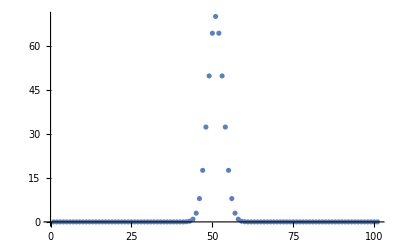

```mathematica
ListPlot[Total[convolintensityfunc[0.2]],PlotRange->All]
```

```mathematica
real=Total[ImageData[-Graphics-]]
```

{22329.,22401.1,22099.,22095.,22759.,22549.,22335.,22429.,22794.,22432.,22547.,22728.,22877.,22950.,22844.9,23504.9,23901.1,24698.,26471.,30867.,38217.,53043.,73689.,98228.,110693.,105898.,86580.,63795.,45644.9,34738.,28041.,25349.1,24400.9,23213.,22933.,22904.,22945.,22718.,22485.,22249.1,22743.,22665.,22339.,22584.,22153.,22448.,22494.,22064.,22448.6}

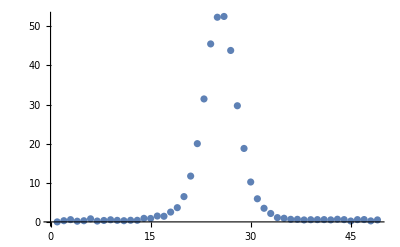

```mathematica
ListPlot[(%400-%400[[1]])/Max[%400]*70,PlotRange->All]
```

```mathematica
ImageAdjust/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

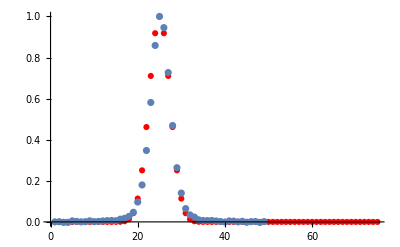

```mathematica
Show[ListPlot[Drop[Total[cov200]/Max[Total[cov200]],26],PlotRange->All,PlotStyle->Red],ListPlot[(real-real[[1]])/Max[real-real[[1]]],PlotRange->All]]
```

```mathematica
convolintensity
```

```mathematica
Total[convolintensity]
```

{6.5899×10^-96,1.14055×10^-91,1.5843×10^-87,1.76629×10^-83,1.58052×10^-79,1.13521×10^-75,6.54492×10^-72,3.02908×10^-68,1.1254×10^-64,3.35684×10^-61,8.03894×10^-58,1.54576×10^-54,2.38667×10^-51,2.95923×10^-48,2.94674×10^-45,2.35679×10^-42,1.51411×10^-39,7.81453×10^-37,3.24047×10^-34,1.07977×10^-31,2.8916×10^-29,6.22449×10^-27,1.07723×10^-24,1.49914×10^-22,1.67808×10^-20,1.51124×10^-18,1.09532×10^-16,6.39129×10^-15,3.00368×10^-13,1.13747×10^-11,3.4729×10^-10,8.55438×10^-9,1.70124×10^-7,2.73417×10^-6,0.0000355509,0.000374481,0.00320101,0.0222496,0.126087,0.584472,2.22561,7.00023,18.3169,40.244,75.1364,121.018,171.245,217.338,252.695,274.229,281.375,274.229,252.695,217.338,171.245,121.018,75.1364,40.244,18.3169,7.00023,2.22561,0.584472,0.126087,0.0222496,0.00320101,0.000374481,0.0000355509,2.73417×10^-6,1.70124×10^-7,8.55438×10^-9,3.4729×10^-10,1.13747×10^-11,3.00368×10^-13,6.39129×10^-15,1.09532×10^-16,1.51124×10^-18,1.67808×10^-20,1.49914×10^-22,1.07723×10^-24,6.22449×10^-27,2.8916×10^-29,1.07977×10^-31,3.24047×10^-34,7.81453×10^-37,1.51411×10^-39,2.35679×10^-42,2.94674×10^-45,2.95923×10^-48,2.38667×10^-51,1.54576×10^-54,8.03894×10^-58,3.35684×10^-61,1.1254×10^-64,3.02908×10^-68,6.54492×10^-72,1.13521×10^-75,1.58052×10^-79,1.76629×10^-83,1.5843×10^-87,1.14055×10^-91,6.5899×10^-96}

```mathematica
Interpolation[Total[convolintensity]]
```

InterpolatingFunction[…]

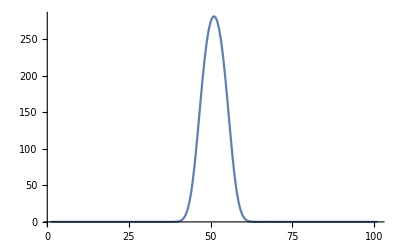

```mathematica
Plot[%424[x],{x,1.,101.},PlotRange->All]
```

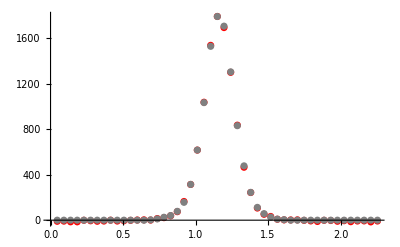
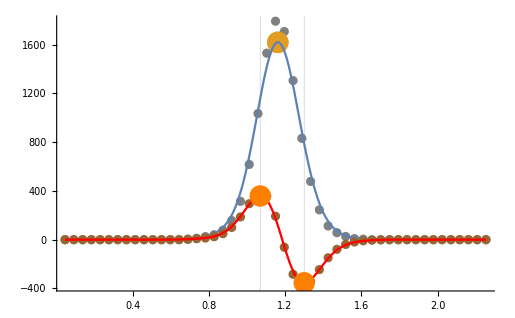
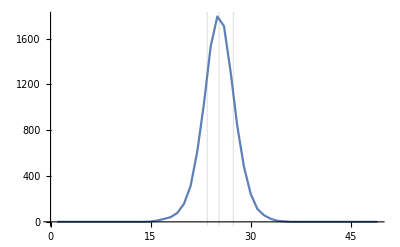
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
allplots[-Graphics-,5]
```

```mathematica
allinfo[-Graphics-,5]
```

{465.382,1619.67,0.230514,0.179821,0.294966,0.736,False,NA,NA,0.046 NA,False,right,0.138484,0.388088,-0.0146364,-0.0188182,0.836273,0.916667,0.401775,0.505821,0.0992338,0.900766}

```mathematica
allinfo[-Graphics-,5]
```

{634.063,13315.2,0.351425,0.254468,0.416291,1.058,False,NA,NA,0.046 NA,False,right,0.196398,0.526644,-0.0125455,0.,0.939817,0.984733,0.825769,0.204181,0.0652228,0.934777}

```mathematica
Total[convolintensity]
```

{6.5899×10^-96,1.14055×10^-91,1.5843×10^-87,1.76629×10^-83,1.58052×10^-79,1.13521×10^-75,6.54492×10^-72,3.02908×10^-68,1.1254×10^-64,3.35684×10^-61,8.03894×10^-58,1.54576×10^-54,2.38667×10^-51,2.95923×10^-48,2.94674×10^-45,2.35679×10^-42,1.51411×10^-39,7.81453×10^-37,3.24047×10^-34,1.07977×10^-31,2.8916×10^-29,6.22449×10^-27,1.07723×10^-24,1.49914×10^-22,1.67808×10^-20,1.51124×10^-18,1.09532×10^-16,6.39129×10^-15,3.00368×10^-13,1.13747×10^-11,3.4729×10^-10,8.55438×10^-9,1.70124×10^-7,2.73417×10^-6,0.0000355509,0.000374481,0.00320101,0.0222496,0.126087,0.584472,2.22561,7.00023,18.3169,40.244,75.1364,121.018,171.245,217.338,252.695,274.229,281.375,274.229,252.695,217.338,171.245,121.018,75.1364,40.244,18.3169,7.00023,2.22561,0.584472,0.126087,0.0222496,0.00320101,0.000374481,0.0000355509,2.73417×10^-6,1.70124×10^-7,8.55438×10^-9,3.4729×10^-10,1.13747×10^-11,3.00368×10^-13,6.39129×10^-15,1.09532×10^-16,1.51124×10^-18,1.67808×10^-20,1.49914×10^-22,1.07723×10^-24,6.22449×10^-27,2.8916×10^-29,1.07977×10^-31,3.24047×10^-34,7.81453×10^-37,1.51411×10^-39,2.35679×10^-42,2.94674×10^-45,2.95923×10^-48,2.38667×10^-51,1.54576×10^-54,8.03894×10^-58,3.35684×10^-61,1.1254×10^-64,3.02908×10^-68,6.54492×10^-72,1.13521×10^-75,1.58052×10^-79,1.76629×10^-83,1.5843×10^-87,1.14055×10^-91,6.5899×10^-96}

```mathematica
MatrixPlot[convolintensity]
```

```mathematica
ImageData[Image[convolintensity]]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,4.2039×10^-45,1.4013×10^-44,3.92364×10^-44,9.10844×10^-44,1.75162×10^-43,2.8026×10^-43,3.71344×10^-43,4.07778×10^-43,3.71344×10^-43,2.8026×10^-43,1.75162×10^-43,9.10844×10^-44,3.92364×10^-44,1.4013×10^-44,4.2039×10^-45,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.8026×10^-45,2.24208×10^-44,1.31722×10^-43,6.51604×10^-43,2.66107×10^-42,9.00054×10^-42,2.52122×10^-41,5.85266×10^-41,1.12628×10^-40,1.79732×10^-40,2.37891×10^-40,2.61189×10^-40,2.37891×10^-40,1.79732×10^-40,1.12628×10^-40,5.85266×10^-41,2.52122×10^-41,9.00054×10^-42,2.66107×10^-42,6.51604×10^-43,1.31722×10^-43,2.24208×10^-44,2.8026×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,1.82169×10^-44,1.91978×10^-43,1.66474×10^-42,1.19208×10^-41,7.05652×10^-41,3.45678×10^-40,1.40228×10^-39,4.71356×10^-39,1.31354×10^-38,3.03616×10^-38,5.82322×10^-38,9.27025×10^-38,1.22521×10^-37,1.34455×10^-37,1.22521×10^-37,9.27025×10^-38,5.82322×10^-38,3.03616×10^-38,1.31354×10^-38,4.71356×10^-39,1.40228×10^-39,3.45678×10^-40,7.05652×10^-41,1.19208×10^-41,1.66474×10^-42,1.91978×10^-43,1.82169×10^-44,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.8026×10^-45,4.2039×10^-44,6.51604×10^-43,8.19619×10^-42,8.50798×10^-41,7.29646×10^-40,5.17402×10^-39,3.03617×10^-38,1.4755×10^-37,5.94269×10^-37,1.98491×10^-36,5.50133×10^-36,1.26586×10^-35,2.41924×10^-35,3.84146×10^-35,5.06925×10^-35,5.56014×10^-35,5.06925×10^-35,3.84146×10^-35,2.41924×10^-35,1.26586×10^-35,5.50133×10^-36,1.98491×10^-36,5.94269×10^-37,1.4755×10^-37,3.03617×10^-38,5.17402×10^-39,7.29646×10^-40,8.50798×10^-41,8.19619×10^-42,6.51604×10^-43,4.2039×10^-44,2.8026×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,3.92364×10^-44,8.632×10^-43,1.5787×10^-41,2.37891×10^-40,2.95738×10^-39,3.03617×10^-38,2.5766×10^-37,1.80914×10^-36,1.05192×10^-35,5.06925×10^-35,2.02625×10^-34,6.72261×10^-34,1.8525×10^-33,4.24226×10^-33,8.07711×10^-33,1.27907×10^-32,1.68512×10^-32,1.84729×10^-32,1.68512×10^-32,1.27907×10^-32,8.07711×10^-33,4.24226×10^-33,1.8525×10^-33,6.72261×10^-34,2.02625×10^-34,5.06925×10^-35,1.05192×10^-35,1.80914×10^-36,2.5766×10^-37,3.03617×10^-38,2.95738×10^-39,2.37891×10^-40,1.5787×10^-41,8.632×10^-43,3.92364×10^-44,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-44,4.47014×10^-43,1.19208×10^-41,2.61189×10^-40,4.71356×10^-39,7.01366×10^-38,8.61391×10^-37,8.74113×10^-36,7.33652×10^-35,5.09799×10^-34,2.93567×10^-33,1.4022×10^-32,5.56001×10^-32,1.83164×10^-31,5.01656×10^-31,1.14298×10^-30,2.16752×10^-30,3.42255×10^-30,4.50123×10^-30,4.93154×10^-30,4.50123×10^-30,3.42255×10^-30,2.16752×10^-30,1.14298×10^-30,5.01656×10^-31,1.83164×10^-31,5.56001×10^-32,1.4022×10^-32,2.93567×10^-33,5.09799×10^-34,7.33652×10^-35,8.74113×10^-36,8.61391×10^-37,7.01366×10^-38,4.71356×10^-39,2.61189×10^-40,1.19208×10^-41,4.47014×10^-43,1.4013×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,9.10844×10^-44,3.52567×10^-42,1.12628×10^-40,2.95738×10^-39,6.39081×10^-38,1.13783×10^-36,1.67094×10^-35,2.02625×10^-34,2.03122×10^-33,1.68512×10^-32,1.15819×10^-31,6.60169×10^-31,3.12378×10^-30,1.22817×10^-29,4.01565×10^-29,1.09271×10^-28,2.47627×10^-28,4.676×10^-28,7.36091×10^-28,9.66292×10^-28,1.05801×10^-27,9.66292×10^-28,7.36091×10^-28,4.676×10^-28,2.47627×10^-28,1.09271×10^-28,4.01565×10^-29,1.22817×10^-29,3.12378×10^-30,6.60169×10^-31,1.15819×10^-31,1.68512×10^-32,2.03122×10^-33,2.02625×10^-34,1.67094×10^-35,1.13783×10^-36,6.39081×10^-38,2.95738×10^-39,1.12628×10^-40,3.52567×10^-42,9.10844×10^-44,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.00649×10^-45,4.07778×10^-43,1.90394×10^-41,7.29646×10^-40,2.29647×10^-38,5.94269×10^-37,1.26586×10^-35,2.22218×10^-34,3.21874×10^-33,3.85147×10^-32,3.81171×10^-31,3.12378×10^-30,2.12233×10^-29,1.19674×10^-28,5.60676×10^-28,2.18464×10^-27,7.08616×10^-27,1.91499×10^-26,4.31486×10^-26,8.11108×10^-26,1.27267×10^-25,1.66739×10^-25,1.82446×10^-25,1.66739×10^-25,1.27267×10^-25,8.11108×10^-26,4.31486×10^-26,1.91499×10^-26,7.08616×10^-27,2.18464×10^-27,5.60676×10^-28,1.19674×10^-28,2.12233×10^-29,3.12378×10^-30,3.81171×10^-31,3.85147×10^-32,3.21874×10^-33,2.22218×10^-34,1.26586×10^-35,5.94269×10^-37,2.29647×10^-38,7.29646×10^-40,1.90394×10^-41,4.07778×10^-43,7.00649×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.82169×10^-44,1.25696×10^-42,7.05652×10^-41,3.2464×10^-39,1.22521×10^-37,3.79773×10^-36,9.6797×10^-35,2.03122×10^-33,3.51361×10^-32,5.01656×10^-31,5.91933×10^-30,5.77977×10^-29,4.676×10^-28,3.1384×10^-27,1.74961×10^-26,8.11108×10^-26,3.13039×10^-25,1.0068×10^-24,2.70091×10^-24,6.0486×10^-24,1.13154×10^-23,1.76927×10^-23,2.31312×10^-23,2.52923×10^-23,2.31312×10^-23,1.76927×10^-23,1.13154×10^-23,6.0486×10^-24,2.70091×10^-24,1.0068×10^-24,3.13039×10^-25,8.11108×10^-26,1.74961×10^-26,3.1384×10^-27,4.676×10^-28,5.77977×10^-29,5.91933×10^-30,5.01656×10^-31,3.51361×10^-32,2.03122×10^-33,9.6797×10^-35,3.79773×10^-36,1.22521×10^-37,3.2464×10^-39,7.05652×10^-41,1.25696×10^-42,1.82169×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.22299×10^-44,2.66107×10^-42,1.79732×10^-40,9.93328×10^-39,4.49816×10^-37,1.67094×10^-35,5.09799×10^-34,1.27907×10^-32,2.64249×10^-31,4.50123×10^-30,6.3305×10^-29,7.36091×10^-28,7.08616×10^-27,5.65554×10^-26,3.74723×10^-25,2.06393×10^-24,9.46194×10^-24,3.61484×10^-23,1.15214×10^-22,3.06673×10^-22,6.82312×10^-22,1.26986×10^-21,1.97816×10^-21,2.58039×10^-21,2.81934×10^-21,2.58039×10^-21,1.97816×10^-21,1.26986×10^-21,6.82312×10^-22,3.06673×10^-22,1.15214×10^-22,3.61484×10^-23,9.46194×10^-24,2.06393×10^-24,3.74723×10^-25,5.65554×10^-26,7.08616×10^-27,7.36091×10^-28,6.3305×10^-29,4.50123×10^-30,2.64249×10^-31,1.27907×10^-32,5.09799×10^-34,1.67094×10^-35,4.49816×10^-37,9.93328×10^-39,1.79732×10^-40,2.66107×10^-42,3.22299×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.92364×10^-44,3.87319×10^-42,3.14849×10^-40,2.09234×10^-38,1.13783×10^-36,5.06925×10^-35,1.8525×10^-33,5.56001×10^-32,1.37236×10^-30,2.78952×10^-29,4.676×10^-28,6.47337×10^-27,7.412×10^-26,7.02966×10^-25,5.5306×10^-24,3.61484×10^-23,1.96566×10^-22,8.9051×10^-22,3.36551×10^-21,1.06238×10^-20,2.80425×10^-20,6.19568×10^-20,1.14673×10^-19,1.77921×10^-19,2.31527×10^-19,2.52761×10^-19,2.31527×10^-19,1.77921×10^-19,1.14673×10^-19,6.19568×10^-20,2.80425×10^-20,1.06238×10^-20,3.36551×10^-21,8.9051×10^-22,1.96566×10^-22,3.61484×10^-23,5.5306×10^-24,7.02966×10^-25,7.412×10^-26,6.47337×10^-27,4.676×10^-28,2.78952×10^-29,1.37236×10^-30,5.56001×10^-32,1.8525×10^-33,5.06925×10^-35,1.13783×10^-36,2.09234×10^-38,3.14849×10^-40,3.87319×10^-42,3.92364×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.22299×10^-44,3.87319×10^-42,3.79522×10^-40,3.03617×10^-38,1.98491×10^-36,1.06164×10^-34,4.65115×10^-33,1.67123×10^-31,4.93154×10^-30,1.19674×10^-28,2.39177×10^-27,3.94264×10^-26,5.36872×10^-25,6.0486×10^-24,5.64717×10^-23,4.3762×10^-22,2.81934×10^-21,1.51239×10^-20,6.76561×10^-20,2.52761×10^-19,7.89707×10^-19,2.06592×10^-18,4.53033×10^-18,8.33536×10^-18,1.28772×10^-17,1.67134×10^-17,1.82304×10^-17,1.67134×10^-17,1.28772×10^-17,8.33536×10^-18,4.53033×10^-18,2.06592×10^-18,7.89707×10^-19,2.52761×10^-19,6.76561×10^-20,1.51239×10^-20,2.81934×10^-21,4.3762×10^-22,5.64717×10^-23,6.0486×10^-24,5.36872×10^-25,3.94264×10^-26,2.39177×10^-27,1.19674×10^-28,4.93154×10^-30,1.67123×10^-31,4.65115×10^-33,1.06164×10^-34,1.98491×10^-36,3.03617×10^-38,3.79522×10^-40,3.87319×10^-42,3.22299×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.82169×10^-44,2.66107×10^-42,3.14849×10^-40,3.03617×10^-38,2.38928×10^-36,1.53606×10^-34,8.07711×10^-33,3.47816×10^-31,1.22817×10^-29,3.5611×10^-28,8.49097×10^-27,1.66739×10^-25,2.70091×10^-24,3.61484×10^-23,4.00407×10^-22,3.677×10^-21,2.80425×10^-20,1.77921×10^-19,9.40742×10^-19,4.15213×10^-18,1.53224×10^-17,4.73468×10^-17,1.22678×10^-16,2.66861×10^-16,4.8787×10^-16,7.50222×10^-16,9.70984×10^-16,1.05812×10^-15,9.70984×10^-16,7.50222×10^-16,4.8787×10^-16,2.66861×10^-16,1.22678×10^-16,4.73468×10^-17,1.53224×10^-17,4.15213×10^-18,9.40742×10^-19,1.77921×10^-19,2.80425×10^-20,3.677×10^-21,4.00407×10^-22,3.61484×10^-23,2.70091×10^-24,1.66739×10^-25,8.49097×10^-27,3.5611×10^-28,1.22817×10^-29,3.47816×10^-31,8.07711×10^-33,1.53606×10^-34,2.38928×10^-36,3.03617×10^-38,3.14849×10^-40,2.66107×10^-42,1.82169×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.00649×10^-45,1.25696×10^-42,1.79732×10^-40,2.09234×10^-38,1.98491×10^-36,1.53606×10^-34,9.70785×10^-33,5.01656×10^-31,2.12233×10^-29,7.36091×10^-28,2.09598×10^-26,4.90726×10^-25,9.46194×10^-24,1.505×10^-22,1.97816×10^-21,2.15246×10^-20,1.94249×10^-19,1.45663×10^-18,9.09328×10^-18,4.73468×10^-17,2.05995×10^-16,7.50222×10^-16,2.29095×10^-15,5.87498×10^-15,1.26695×10^-14,2.30029×10^-14,3.51962×10^-14,4.5415×10^-14,4.94401×10^-14,4.5415×10^-14,3.51962×10^-14,2.30029×10^-14,1.26695×10^-14,5.87498×10^-15,2.29095×10^-15,7.50222×10^-16,2.05995×10^-16,4.73468×10^-17,9.09328×10^-18,1.45663×10^-18,1.94249×10^-19,2.15246×10^-20,1.97816×10^-21,1.505×10^-22,9.46194×10^-24,4.90726×10^-25,2.09598×10^-26,7.36091×10^-28,2.12233×10^-29,5.01656×10^-31,9.70785×10^-33,1.53606×10^-34,1.98491×10^-36,2.09234×10^-38,1.79732×10^-40,1.25696×10^-42,7.00649×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,4.07778×10^-43,7.05652×10^-41,9.93328×10^-39,1.13783×10^-36,1.06164×10^-34,8.07711×10^-33,5.01656×10^-31,2.54661×10^-29,1.05801×10^-27,3.60249×10^-26,1.0068×10^-24,2.31312×10^-23,4.3762×10^-22,6.82972×10^-21,8.80879×10^-20,9.40742×10^-19,8.33536×10^-18,6.13986×10^-17,3.76759×10^-16,1.92988×10^-15,8.26874×10^-15,2.96922×10^-14,8.95256×10^-14,2.27042×10^-13,4.85053×10^-13,8.74128×10^-13,1.33025×10^-12,1.71083×10^-12,1.8604×10^-12,1.71083×10^-12,1.33025×10^-12,8.74128×10^-13,4.85053×10^-13,2.27042×10^-13,8.95256×10^-14,2.96922×10^-14,8.26874×10^-15,1.92988×10^-15,3.76759×10^-16,6.13986×10^-17,8.33536×10^-18,9.40742×10^-19,8.80879×10^-20,6.82972×10^-21,4.3762×10^-22,2.31312×10^-23,1.0068×10^-24,3.60249×10^-26,1.05801×10^-27,2.54661×10^-29,5.01656×10^-31,8.07711×10^-33,1.06164×10^-34,1.13783×10^-36,9.93328×10^-39,7.05652×10^-41,4.07778×10^-43,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,9.10844×10^-44,1.90394×10^-41,3.2464×10^-39,4.49816×10^-37,5.06925×10^-35,4.65115×10^-33,3.47816×10^-31,2.12233×10^-29,1.05801×10^-27,4.31486×10^-26,1.44166×10^-24,3.95229×10^-23,8.9051×10^-22,1.65193×10^-20,2.52761×10^-19,3.19628×10^-18,3.3472×10^-17,2.90899×10^-16,2.10271×10^-15,1.26695×10^-14,6.37761×10^-14,2.68811×10^-13,9.50758×10^-13,2.82769×10^-12,7.08555×10^-12,1.49849×10^-11,2.67872×10^-11,4.05252×10^-11,5.19331×10^-11,5.64057×10^-11,5.19331×10^-11,4.05252×10^-11,2.67872×10^-11,1.49849×10^-11,7.08555×10^-12,2.82769×10^-12,9.50758×10^-13,2.68811×10^-13,6.37761×10^-14,1.26695×10^-14,2.10271×10^-15,2.90899×10^-16,3.3472×10^-17,3.19628×10^-18,2.52761×10^-19,1.65193×10^-20,8.9051×10^-22,3.95229×10^-23,1.44166×10^-24,4.31486×10^-26,1.05801×10^-27,2.12233×10^-29,3.47816×10^-31,4.65115×10^-33,5.06925×10^-35,4.49816×10^-37,3.2464×10^-39,1.90394×10^-41,9.10844×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-44,3.52567×10^-42,7.29646×10^-40,1.22521×10^-37,1.67094×10^-35,1.8525×10^-33,1.67123×10^-31,1.22817×10^-29,7.36091×10^-28,3.60249×10^-26,1.44166×10^-24,4.72446×10^-23,1.26986×10^-21,2.80425×10^-20,5.09711×10^-19,7.64048×10^-18,9.4646×10^-17,9.70984×10^-16,8.26874×10^-15,5.8588×10^-14,3.46238×10^-13,1.71083×10^-12,7.08555×10^-12,2.46562×10^-11,7.22567×10^-11,1.7872×10^-10,3.73831×10^-10,6.6241×10^-10,9.95721×10^-10,1.27104×10^-9,1.37869×10^-9,1.27104×10^-9,9.95721×10^-10,6.6241×10^-10,3.73831×10^-10,1.7872×10^-10,7.22567×10^-11,2.46562×10^-11,7.08555×10^-12,1.71083×10^-12,3.46238×10^-13,5.8588×10^-14,8.26874×10^-15,9.70984×10^-16,9.4646×10^-17,7.64048×10^-18,5.09711×10^-19,2.80425×10^-20,1.26986×10^-21,4.72446×10^-23,1.44166×10^-24,3.60249×10^-26,7.36091×10^-28,1.22817×10^-29,1.67123×10^-31,1.8525×10^-33,1.67094×10^-35,1.22521×10^-37,7.29646×10^-40,3.52567×10^-42,1.4013×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,4.47014×10^-43,1.12628×10^-40,2.29647×10^-38,3.79773×10^-36,5.09799×10^-34,5.56001×10^-32,4.93154×10^-30,3.5611×10^-28,2.09598×10^-26,1.0068×10^-24,3.95229×10^-23,1.26986×10^-21,3.34481×10^-20,7.23524×10^-19,1.28772×10^-17,1.88957×10^-16,2.29096×10^-15,2.30029×10^-14,1.91743×10^-13,1.33025×10^-12,7.70134×10^-12,3.73072×10^-11,1.51633×10^-10,5.18487×10^-10,1.49541×10^-9,3.647×10^-9,7.53766×10^-9,1.32287×10^-8,1.9746×10^-8,2.50982×10^-8,2.71849×10^-8,2.50982×10^-8,1.9746×10^-8,1.32287×10^-8,7.53766×10^-9,3.647×10^-9,1.49541×10^-9,5.18487×10^-10,1.51633×10^-10,3.73072×10^-11,7.70134×10^-12,1.33025×10^-12,1.91743×10^-13,2.30029×10^-14,2.29096×10^-15,1.88957×10^-16,1.28772×10^-17,7.23524×10^-19,3.34481×10^-20,1.26986×10^-21,3.95229×10^-23,1.0068×10^-24,2.09598×10^-26,3.5611×10^-28,4.93154×10^-30,5.56001×10^-32,5.09799×10^-34,3.79773×10^-36,2.29647×10^-38,1.12628×10^-40,4.47014×10^-43,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.92364×10^-44,1.19208×10^-41,2.95738×10^-39,5.94269×10^-37,9.6797×10^-35,1.27907×10^-32,1.37236×10^-30,1.19674×10^-28,8.49097×10^-27,4.90726×10^-25,2.31312×10^-23,8.90443×10^-22,2.80425×10^-20,7.23524×10^-19,1.53224×10^-17,2.66861×10^-16,3.83042×10^-15,4.5415×10^-14,4.45864×10^-13,3.63397×10^-12,2.46562×10^-11,1.39663×10^-10,6.6241×10^-10,2.63858×10^-9,8.85355×10^-9,2.50982×10^-8,6.02783×10^-8,1.22967×10^-7,2.13554×10^-7,3.16318×10^-7,4.0017×10^-7,4.32756×10^-7,4.0017×10^-7,3.16318×10^-7,2.13554×10^-7,1.22967×10^-7,6.02783×10^-8,2.50982×10^-8,8.85355×10^-9,2.63858×10^-9,6.6241×10^-10,1.39663×10^-10,2.46562×10^-11,3.63397×10^-12,4.45864×10^-13,4.5415×10^-14,3.83042×10^-15,2.66861×10^-16,1.53224×10^-17,7.23524×10^-19,2.80425×10^-20,8.90443×10^-22,2.31312×10^-23,4.90726×10^-25,8.49097×10^-27,1.19674×10^-28,1.37236×10^-30,1.27907×10^-32,9.6797×10^-35,5.94269×10^-37,2.95738×10^-39,1.19208×10^-41,3.92364×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.8026×10^-45,8.632×10^-43,2.61189×10^-40,6.39081×10^-38,1.26586×10^-35,2.03122×10^-33,2.64249×10^-31,2.78952×10^-29,2.39177×10^-27,1.66739×10^-25,9.46194×10^-24,4.3762×10^-22,1.65193×10^-20,5.09711×10^-19,1.28772×10^-17,2.66861×10^-16,4.54548×10^-15,6.37761×10^-14,7.38841×10^-13,7.08555×10^-12,5.64057×10^-11,3.73831×10^-10,2.06908×10^-9,9.59472×10^-9,3.74011×10^-8,1.22967×10^-7,3.42125×10^-7,8.08079×10^-7,1.62508×10^-6,2.78986×10^-6,4.09748×10^-6,5.15685×10^-6,5.56704×10^-6,5.15685×10^-6,4.09748×10^-6,2.78986×10^-6,1.62508×10^-6,8.08079×10^-7,3.42125×10^-7,1.22967×10^-7,3.74011×10^-8,9.59472×10^-9,2.06908×10^-9,3.73831×10^-10,5.64057×10^-11,7.08555×10^-12,7.38841×10^-13,6.37761×10^-14,4.54548×10^-15,2.66861×10^-16,1.28772×10^-17,5.09711×10^-19,1.65193×10^-20,4.3762×10^-22,9.46194×10^-24,1.66739×10^-25,2.39177×10^-27,2.78952×10^-29,2.64249×10^-31,2.03122×10^-33,1.26586×10^-35,6.39081×10^-38,2.61189×10^-40,8.632×10^-43,2.8026×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.2039×10^-44,1.5787×10^-41,4.71356×10^-39,1.13783×10^-36,2.22218×10^-34,3.51361×10^-32,4.50123×10^-30,4.676×10^-28,3.94264×10^-26,2.70091×10^-24,1.505×10^-22,6.82972×10^-21,2.52761×10^-19,7.64048×10^-18,1.88957×10^-16,3.83042×10^-15,6.37761×10^-14,8.74128×10^-13,9.88711×10^-12,9.25356×10^-11,7.1872×10^-10,4.64714×10^-9,2.50982×10^-8,1.13622×10^-7,4.32756×10^-7,1.39189×10^-6,3.79471×10^-6,8.80102×10^-6,0.0000174239,0.0000295349,0.0000429734,0.0000537741,0.0000579391,0.0000537741,0.0000429734,0.0000295349,0.0000174239,8.80102×10^-6,3.79471×10^-6,1.39189×10^-6,4.32756×10^-7,1.13622×10^-7,2.50982×10^-8,4.64714×10^-9,7.1872×10^-10,9.25356×10^-11,9.88711×10^-12,8.74128×10^-13,6.37761×10^-14,3.83042×10^-15,1.88957×10^-16,7.64048×10^-18,2.52761×10^-19,6.82972×10^-21,1.505×10^-22,2.70091×10^-24,3.94264×10^-26,4.676×10^-28,4.50123×10^-30,3.51361×10^-32,2.22218×10^-34,1.13783×10^-36,4.71356×10^-39,1.5787×10^-41,4.2039×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,6.51604×10^-43,2.37891×10^-40,7.01366×10^-38,1.67094×10^-35,3.21874×10^-33,5.01656×10^-31,6.3305×10^-29,6.47337×10^-27,5.36872×10^-25,3.61484×10^-23,1.97816×10^-21,8.80879×10^-20,3.19628×10^-18,9.4646×10^-17,2.29096×10^-15,4.5415×10^-14,7.38841×10^-13,9.88711×10^-12,1.09109×10^-10,9.95721×10^-10,7.53766×10^-9,4.74905×10^-8,2.49928×10^-7,1.10289×10^-6,4.09748×10^-6,0.0000128701,0.0000343215,0.0000780314,0.000151844,0.000253798,0.000365461,0.000454401,0.000488542,0.000454401,0.000365461,0.000253798,0.000151844,0.0000780314,0.0000343215,0.0000128701,4.09748×10^-6,1.10289×10^-6,2.49928×10^-7,4.74905×10^-8,7.53766×10^-9,9.95721×10^-10,1.09109×10^-10,9.88711×10^-12,7.38841×10^-13,4.5415×10^-14,2.29096×10^-15,9.4646×10^-17,3.19628×10^-18,8.80879×10^-20,1.97816×10^-21,3.61484×10^-23,5.36872×10^-25,6.47337×10^-27,6.3305×10^-29,5.01656×10^-31,3.21874×10^-33,1.67094×10^-35,7.01366×10^-38,2.37891×10^-40,6.51604×10^-43,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.82169×10^-44,8.19619×10^-42,2.95738×10^-39,8.61391×10^-37,2.02625×10^-34,3.85147×10^-32,5.91933×10^-30,7.36091×10^-28,7.412×10^-26,6.0486×10^-24,4.00406×10^-22,2.15246×10^-20,9.40742×10^-19,3.3472×10^-17,9.70984×10^-16,2.30029×10^-14,4.45864×10^-13,7.08555×10^-12,9.25356×10^-11,9.95721×10^-10,8.85355×10^-9,6.52592×10^-8,4.0017×10^-7,2.04929×10^-6,8.80102×10^-6,0.0000318394,0.0000974821,0.000253798,0.000564574,0.00107796,0.00177393,0.00252502,0.00311721,0.00334335,0.00311721,0.00252502,0.00177393,0.00107796,0.000564574,0.000253798,0.0000974821,0.0000318394,8.80102×10^-6,2.04929×10^-6,4.0017×10^-7,6.52592×10^-8,8.85355×10^-9,9.95721×10^-10,9.25356×10^-11,7.08555×10^-12,4.45864×10^-13,2.30029×10^-14,9.70984×10^-16,3.3472×10^-17,9.40742×10^-19,2.15246×10^-20,4.00406×10^-22,6.0486×10^-24,7.412×10^-26,7.36091×10^-28,5.91933×10^-30,3.85147×10^-32,2.02625×10^-34,8.61391×10^-37,2.95738×10^-39,8.19619×10^-42,1.82169×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.91978×10^-43,8.50798×10^-41,3.03616×10^-38,8.74115×10^-36,2.03122×10^-33,3.81171×10^-31,5.77977×10^-29,7.08616×10^-27,7.02966×10^-25,5.64717×10^-23,3.67699×10^-21,1.94249×10^-19,8.33536×10^-18,2.90899×10^-16,8.26874×10^-15,1.91743×10^-13,3.63397×10^-12,5.64057×10^-11,7.1872×10^-10,7.53766×10^-9,6.52592×10^-8,4.67972×10^-7,2.78986×10^-6,0.000013884,0.0000579391,0.000203739,0.000606843,0.0015393,0.00334335,0.00625117,0.010111,0.0142073,0.0173997,0.0186116,0.0173997,0.0142073,0.010111,0.00625117,0.00334335,0.0015393,0.000606843,0.000203739,0.0000579391,0.000013884,2.78986×10^-6,4.67972×10^-7,6.52592×10^-8,7.53766×10^-9,7.1872×10^-10,5.64057×10^-11,3.63397×10^-12,1.91743×10^-13,8.26874×10^-15,2.90899×10^-16,8.33536×10^-18,1.94249×10^-19,3.67699×10^-21,5.64717×10^-23,7.02966×10^-25,7.08616×10^-27,5.77977×10^-29,3.81171×10^-31,2.03122×10^-33,8.74115×10^-36,3.03616×10^-38,8.50798×10^-41,1.91978×10^-43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.8026×10^-45,1.66474×10^-42,7.29646×10^-40,2.5766×10^-37,7.33652×10^-35,1.68512×10^-32,3.12378×10^-30,4.676×10^-28,5.65554×10^-26,5.5306×10^-24,4.3762×10^-22,2.80425×10^-20,1.45663×10^-18,6.13986×10^-17,2.10271×10^-15,5.8588×10^-14,1.33025×10^-12,2.46562×10^-11,3.73831×10^-10,4.64714×10^-9,4.74905×10^-8,4.0017×10^-7,2.78986×10^-6,0.0000161546,0.0000780314,0.000315938,0.00107796,0.00311721,0.00768675,0.0162649,0.0297154,0.0471479,0.0652985,0.0792556,0.0845173,0.0792556,0.0652985,0.0471479,0.0297154,0.0162649,0.00768675,0.00311721,0.00107796,0.000315938,0.0000780314,0.0000161546,2.78986×10^-6,4.0017×10^-7,4.74905×10^-8,4.64714×10^-9,3.73831×10^-10,2.46562×10^-11,1.33025×10^-12,5.8588×10^-14,2.10271×10^-15,6.13986×10^-17,1.45663×10^-18,2.80425×10^-20,4.3762×10^-22,5.5306×10^-24,5.65554×10^-26,4.676×10^-28,3.12378×10^-30,1.68512×10^-32,7.33652×10^-35,2.5766×10^-37,7.29646×10^-40,1.66474×10^-42,2.8026×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.24208×10^-44,1.19208×10^-41,5.17402×10^-39,1.80914×10^-36,5.09799×10^-34,1.15819×10^-31,2.12233×10^-29,3.1384×10^-27,3.74723×10^-25,3.61484×10^-23,2.81934×10^-21,1.77921×10^-19,9.09328×10^-18,3.76759×10^-16,1.26695×10^-14,3.46238×10^-13,7.70134×10^-12,1.39663×10^-10,2.06908×10^-9,2.50982×10^-8,2.49928×10^-7,2.04929×10^-6,0.000013884,0.0000780314,0.000365461,0.00143369,0.0047382,0.013276,0.0317535,0.0652985,0.116292,0.180607,0.246113,0.295708,0.314255,0.295708,0.246113,0.180607,0.116292,0.0652985,0.0317535,0.013276,0.0047382,0.00143369,0.000365461,0.0000780314,0.000013884,2.04929×10^-6,2.49928×10^-7,2.50982×10^-8,2.06908×10^-9,1.39663×10^-10,7.70134×10^-12,3.46238×10^-13,1.26695×10^-14,3.76759×10^-16,9.09328×10^-18,1.77921×10^-19,2.81934×10^-21,3.61484×10^-23,3.74723×10^-25,3.1384×10^-27,2.12233×10^-29,1.15819×10^-31,5.09799×10^-34,1.80914×10^-36,5.17402×10^-39,1.19208×10^-41,2.24208×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.31722×10^-43,7.05652×10^-41,3.03616×10^-38,1.05192×10^-35,2.93567×10^-33,6.60169×10^-31,1.19674×10^-28,1.74961×10^-26,2.06393×10^-24,1.96566×10^-22,1.51239×10^-20,9.40742×10^-19,4.73468×10^-17,1.92988×10^-15,6.37761×10^-14,1.71083×10^-12,3.73072×10^-11,6.6241×10^-10,9.59472×10^-9,1.13622×10^-7,1.10289×10^-6,8.80102×10^-6,0.0000579391,0.000315938,0.00143369,0.0054435,0.0173997,0.0471479,0.109134,0.21757,0.376751,0.571364,0.764574,0.908208,0.961414,0.908208,0.764574,0.571364,0.376751,0.21757,0.109134,0.0471479,0.0173997,0.0054435,0.00143369,0.000315938,0.0000579391,8.80102×10^-6,1.10289×10^-6,1.13622×10^-7,9.59472×10^-9,6.6241×10^-10,3.73072×10^-11,1.71083×10^-12,6.37761×10^-14,1.92988×10^-15,4.73468×10^-17,9.40742×10^-19,1.51239×10^-20,1.96566×10^-22,2.06393×10^-24,1.74961×10^-26,1.19674×10^-28,6.60169×10^-31,2.93567×10^-33,1.05192×10^-35,3.03616×10^-38,7.05652×10^-41,1.31722×10^-43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,6.51604×10^-43,3.45678×10^-40,1.4755×10^-37,5.06925×10^-35,1.4022×10^-32,3.12378×10^-30,5.60675×10^-28,8.11108×10^-26,9.46194×10^-24,8.9051×10^-22,6.76561×10^-20,4.15213×10^-18,2.05995×10^-16,8.26874×10^-15,2.68811×10^-13,7.08555×10^-12,1.51633×10^-10,2.63858×10^-9,3.74011×10^-8,4.32756×10^-7,4.09748×10^-6,0.0000318394,0.000203739,0.00107796,0.0047382,0.0173997,0.0537303,0.140574,0.314255,0.605897,1.0175,1.50304,1.97087,2.31121,2.43586,2.31121,1.97087,1.50304,1.0175,0.605897,0.314255,0.140574,0.0537303,0.0173997,0.0047382,0.00107796,0.000203739,0.0000318394,4.09748×10^-6,4.32756×10^-7,3.74011×10^-8,2.63858×10^-9,1.51633×10^-10,7.08555×10^-12,2.68811×10^-13,8.26874×10^-15,2.05995×10^-16,4.15213×10^-18,6.76561×10^-20,8.9051×10^-22,9.46194×10^-24,8.11108×10^-26,5.60675×10^-28,3.12378×10^-30,1.4022×10^-32,5.06925×10^-35,1.4755×10^-37,3.45678×10^-40,6.51604×10^-43,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.2039×10^-45,2.66107×10^-42,1.40228×10^-39,5.94269×10^-37,2.02625×10^-34,5.56001×10^-32,1.22817×10^-29,2.18464×10^-27,3.13039×10^-25,3.61484×10^-23,3.36551×10^-21,2.52761×10^-19,1.53224×10^-17,7.50222×10^-16,2.96922×10^-14,9.50758×10^-13,2.46562×10^-11,5.18487×10^-10,8.85355×10^-9,1.22967×10^-7,1.39189×10^-6,0.0000128701,0.0000974821,0.000606843,0.00311721,0.013276,0.0471479,0.140574,0.354714,0.764574,1.42262,2.31121,3.31715,4.25288,4.91615,5.15571,4.91615,4.25288,3.31715,2.31121,1.42262,0.764574,0.354714,0.140574,0.0471479,0.013276,0.00311721,0.000606843,0.0000974821,0.0000128701,1.39189×10^-6,1.22967×10^-7,8.85355×10^-9,5.18487×10^-10,2.46562×10^-11,9.50758×10^-13,2.96922×10^-14,7.50222×10^-16,1.53224×10^-17,2.52761×10^-19,3.36551×10^-21,3.61484×10^-23,3.13039×10^-25,2.18464×10^-27,1.22817×10^-29,5.56001×10^-32,2.02625×10^-34,5.94269×10^-37,1.40228×10^-39,2.66107×10^-42,4.2039×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-44,9.00054×10^-42,4.71356×10^-39,1.98491×10^-36,6.72261×10^-34,1.83164×10^-31,4.01565×10^-29,7.08616×10^-27,1.0068×10^-24,1.15214×10^-22,1.06238×10^-20,7.89707×10^-19,4.73468×10^-17,2.29096×10^-15,8.95256×10^-14,2.82769×10^-12,7.22567×10^-11,1.49541×10^-9,2.50982×10^-8,3.42125×10^-7,3.79471×10^-6,0.0000343215,0.000253798,0.0015393,0.00768675,0.0317535,0.109134,0.314255,0.764574,1.58759,2.8465,4.46498,6.21268,7.77217,8.84328,9.22358,8.84328,7.77217,6.21268,4.46498,2.8465,1.58759,0.764574,0.314255,0.109134,0.0317535,0.00768675,0.0015393,0.000253798,0.0000343215,3.79471×10^-6,3.42125×10^-7,2.50982×10^-8,1.49541×10^-9,7.22567×10^-11,2.82769×10^-12,8.95256×10^-14,2.29096×10^-15,4.73468×10^-17,7.89707×10^-19,1.06238×10^-20,1.15214×10^-22,1.0068×10^-24,7.08616×10^-27,4.01565×10^-29,1.83164×10^-31,6.72261×10^-34,1.98491×10^-36,4.71356×10^-39,9.00054×10^-42,1.4013×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.92364×10^-44,2.52122×10^-41,1.31354×10^-38,5.50133×10^-36,1.8525×10^-33,5.01656×10^-31,1.09271×10^-28,1.91499×10^-26,2.70091×10^-24,3.06673×10^-22,2.80425×10^-20,2.06592×10^-18,1.22678×10^-16,5.87498×10^-15,2.27042×10^-13,7.08555×10^-12,1.7872×10^-10,3.647×10^-9,6.02783×10^-8,8.08079×10^-7,8.80102×10^-6,0.0000780314,0.000564574,0.00334335,0.0162649,0.0652985,0.21757,0.605897,1.42262,2.8465,4.91615,7.43808,10.0194,12.2124,13.6618,14.1656,13.6618,12.2124,10.0194,7.43808,4.91615,2.8465,1.42262,0.605897,0.21757,0.0652985,0.0162649,0.00334335,0.000564574,0.0000780314,8.80102×10^-6,8.08079×10^-7,6.02783×10^-8,3.647×10^-9,1.7872×10^-10,7.08555×10^-12,2.27042×10^-13,5.87498×10^-15,1.22678×10^-16,2.06592×10^-18,2.80425×10^-20,3.06673×10^-22,2.70091×10^-24,1.91499×10^-26,1.09271×10^-28,5.01656×10^-31,1.8525×10^-33,5.50133×10^-36,1.31354×10^-38,2.52122×10^-41,3.92364×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,9.10844×10^-44,5.85266×10^-41,3.03617×10^-38,1.26586×10^-35,4.24226×10^-33,1.14298×10^-30,2.47627×10^-28,4.31486×10^-26,6.0486×10^-24,6.82312×10^-22,6.19568×10^-20,4.53033×10^-18,2.66861×10^-16,1.26695×10^-14,4.85053×10^-13,1.49849×10^-11,3.73831×10^-10,7.53766×10^-9,1.22967×10^-7,1.62508×10^-6,0.0000174239,0.000151844,0.00107796,0.00625117,0.0297154,0.116292,0.376751,1.0175,2.31121,4.46498,7.43808,10.8621,14.1656,16.8168,18.4889,19.0545,18.4889,16.8168,14.1656,10.8621,7.43808,4.46498,2.31121,1.0175,0.376751,0.116292,0.0297154,0.00625117,0.00107796,0.000151844,0.0000174239,1.62508×10^-6,1.22967×10^-7,7.53766×10^-9,3.73831×10^-10,1.49849×10^-11,4.85053×10^-13,1.26695×10^-14,2.66861×10^-16,4.53033×10^-18,6.19568×10^-20,6.82312×10^-22,6.0486×10^-24,4.31486×10^-26,2.47627×10^-28,1.14298×10^-30,4.24226×10^-33,1.26586×10^-35,3.03617×10^-38,5.85266×10^-41,9.10844×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.75162×10^-43,1.12628×10^-40,5.82322×10^-38,2.41924×10^-35,8.07711×10^-33,2.16752×10^-30,4.676×10^-28,8.11108×10^-26,1.13154×10^-23,1.26986×10^-21,1.14673×10^-19,8.33536×10^-18,4.8787×10^-16,2.30029×10^-14,8.74128×10^-13,2.67872×10^-11,6.6241×10^-10,1.32287×10^-8,2.13554×10^-7,2.78986×10^-6,0.0000295349,0.000253798,0.00177393,0.010111,0.0471479,0.180607,0.571364,1.50304,3.31715,6.21268,10.0194,14.1656,17.9268,20.7603,22.451,23.004,22.451,20.7603,17.9268,14.1656,10.0194,6.21268,3.31715,1.50304,0.571364,0.180607,0.0471479,0.010111,0.00177393,0.000253798,0.0000295349,2.78986×10^-6,2.13554×10^-7,1.32287×10^-8,6.6241×10^-10,2.67872×10^-11,8.74128×10^-13,2.30029×10^-14,4.8787×10^-16,8.33536×10^-18,1.14673×10^-19,1.26986×10^-21,1.13154×10^-23,8.11108×10^-26,4.676×10^-28,2.16752×10^-30,8.07711×10^-33,2.41924×10^-35,5.82322×10^-38,1.12628×10^-40,1.75162×10^-43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.8026×10^-43,1.79732×10^-40,9.27027×10^-38,3.84146×10^-35,1.27907×10^-32,3.42255×10^-30,7.36091×10^-28,1.27267×10^-25,1.76927×10^-23,1.97816×10^-21,1.77921×10^-19,1.28772×10^-17,7.50223×10^-16,3.51962×10^-14,1.33025×10^-12,4.05252×10^-11,9.95721×10^-10,1.9746×10^-8,3.16318×10^-7,4.09748×10^-6,0.0000429734,0.000365461,0.00252502,0.0142073,0.0652985,0.246113,0.764574,1.97087,4.25288,7.77217,12.2124,16.8168,20.7603,23.5489,25.1156,25.6085,25.1156,23.5489,20.7603,16.8168,12.2124,7.77217,4.25288,1.97087,0.764574,0.246113,0.0652985,0.0142073,0.00252502,0.000365461,0.0000429734,4.09748×10^-6,3.16318×10^-7,1.9746×10^-8,9.95721×10^-10,4.05252×10^-11,1.33025×10^-12,3.51962×10^-14,7.50223×10^-16,1.28772×10^-17,1.77921×10^-19,1.97816×10^-21,1.76927×10^-23,1.27267×10^-25,7.36091×10^-28,3.42255×10^-30,1.27907×10^-32,3.84146×10^-35,9.27027×10^-38,1.79732×10^-40,2.8026×10^-43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.71344×10^-43,2.37891×10^-40,1.22521×10^-37,5.06925×10^-35,1.68512×10^-32,4.50123×10^-30,9.66292×10^-28,1.66739×10^-25,2.31312×10^-23,2.58039×10^-21,2.31527×10^-19,1.67134×10^-17,9.70984×10^-16,4.5415×10^-14,1.71083×10^-12,5.19331×10^-11,1.27104×10^-9,2.50982×10^-8,4.0017×10^-7,5.15685×10^-6,0.0000537741,0.000454401,0.00311721,0.0173997,0.0792556,0.295708,0.908208,2.31121,4.91615,8.84328,13.6618,18.4889,22.451,25.1156,26.5375,26.9691,26.5375,25.1156,22.451,18.4889,13.6618,8.84328,4.91615,2.31121,0.908208,0.295708,0.0792556,0.0173997,0.00311721,0.000454401,0.0000537741,5.15685×10^-6,4.0017×10^-7,2.50982×10^-8,1.27104×10^-9,5.19331×10^-11,1.71083×10^-12,4.5415×10^-14,9.70984×10^-16,1.67134×10^-17,2.31527×10^-19,2.58039×10^-21,2.31312×10^-23,1.66739×10^-25,9.66292×10^-28,4.50123×10^-30,1.68512×10^-32,5.06925×10^-35,1.22521×10^-37,2.37891×10^-40,3.71344×10^-43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.07778×10^-43,2.61189×10^-40,1.34455×10^-37,5.56014×10^-35,1.84729×10^-32,4.93154×10^-30,1.05801×10^-27,1.82446×10^-25,2.52923×10^-23,2.81934×10^-21,2.52761×10^-19,1.82304×10^-17,1.05812×10^-15,4.94401×10^-14,1.8604×10^-12,5.64057×10^-11,1.37869×10^-9,2.71849×10^-8,4.32756×10^-7,5.56704×10^-6,0.0000579391,0.000488542,0.00334335,0.0186116,0.0845173,0.314255,0.961412,2.43586,5.15571,9.22358,14.1656,19.0545,23.004,25.6085,26.9691,27.3757,26.9691,25.6085,23.004,19.0545,14.1656,9.22358,5.15571,2.43586,0.961412,0.314255,0.0845173,0.0186116,0.00334335,0.000488542,0.0000579391,5.56704×10^-6,4.32756×10^-7,2.71849×10^-8,1.37869×10^-9,5.64057×10^-11,1.8604×10^-12,4.94401×10^-14,1.05812×10^-15,1.82304×10^-17,2.52761×10^-19,2.81934×10^-21,2.52923×10^-23,1.82446×10^-25,1.05801×10^-27,4.93154×10^-30,1.84729×10^-32,5.56014×10^-35,1.34455×10^-37,2.61189×10^-40,4.07778×10^-43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.71344×10^-43,2.37891×10^-40,1.22521×10^-37,5.06925×10^-35,1.68512×10^-32,4.50123×10^-30,9.66292×10^-28,1.66739×10^-25,2.31312×10^-23,2.58039×10^-21,2.31527×10^-19,1.67134×10^-17,9.70984×10^-16,4.5415×10^-14,1.71083×10^-12,5.19331×10^-11,1.27104×10^-9,2.50982×10^-8,4.0017×10^-7,5.15685×10^-6,0.0000537741,0.000454401,0.00311721,0.0173997,0.0792556,0.295708,0.908208,2.31121,4.91615,8.84328,13.6618,18.4889,22.451,25.1156,26.5375,26.9691,26.5375,25.1156,22.451,18.4889,13.6618,8.84328,4.91615,2.31121,0.908208,0.295708,0.0792556,0.0173997,0.00311721,0.000454401,0.0000537741,5.15685×10^-6,4.0017×10^-7,2.50982×10^-8,1.27104×10^-9,5.19331×10^-11,1.71083×10^-12,4.5415×10^-14,9.70984×10^-16,1.67134×10^-17,2.31527×10^-19,2.58039×10^-21,2.31312×10^-23,1.66739×10^-25,9.66292×10^-28,4.50123×10^-30,1.68512×10^-32,5.06925×10^-35,1.22521×10^-37,2.37891×10^-40,3.71344×10^-43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.8026×10^-43,1.79732×10^-40,9.27027×10^-38,3.84146×10^-35,1.27907×10^-32,3.42255×10^-30,7.36091×10^-28,1.27267×10^-25,1.76927×10^-23,1.97816×10^-21,1.77921×10^-19,1.28772×10^-17,7.50223×10^-16,3.51962×10^-14,1.33025×10^-12,4.05252×10^-11,9.95721×10^-10,1.9746×10^-8,3.16318×10^-7,4.09748×10^-6,0.0000429734,0.000365461,0.00252502,0.0142073,0.0652985,0.246113,0.764574,1.97087,4.25288,7.77217,12.2124,16.8168,20.7603,23.5489,25.1156,25.6085,25.1156,23.5489,20.7603,16.8168,12.2124,7.77217,4.25288,1.97087,0.764574,0.246113,0.0652985,0.0142073,0.00252502,0.000365461,0.0000429734,4.09748×10^-6,3.16318×10^-7,1.9746×10^-8,9.95721×10^-10,4.05252×10^-11,1.33025×10^-12,3.51962×10^-14,7.50223×10^-16,1.28772×10^-17,1.77921×10^-19,1.97816×10^-21,1.76927×10^-23,1.27267×10^-25,7.36091×10^-28,3.42255×10^-30,1.27907×10^-32,3.84146×10^-35,9.27027×10^-38,1.79732×10^-40,2.8026×10^-43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.75162×10^-43,1.12628×10^-40,5.82322×10^-38,2.41924×10^-35,8.07711×10^-33,2.16752×10^-30,4.676×10^-28,8.11108×10^-26,1.13154×10^-23,1.26986×10^-21,1.14673×10^-19,8.33536×10^-18,4.8787×10^-16,2.30029×10^-14,8.74128×10^-13,2.67872×10^-11,6.6241×10^-10,1.32287×10^-8,2.13554×10^-7,2.78986×10^-6,0.0000295349,0.000253798,0.00177393,0.010111,0.0471479,0.180607,0.571364,1.50304,3.31715,6.21268,10.0194,14.1656,17.9268,20.7603,22.451,23.004,22.451,20.7603,17.9268,14.1656,10.0194,6.21268,3.31715,1.50304,0.571364,0.180607,0.0471479,0.010111,0.00177393,0.000253798,0.0000295349,2.78986×10^-6,2.13554×10^-7,1.32287×10^-8,6.6241×10^-10,2.67872×10^-11,8.74128×10^-13,2.30029×10^-14,4.8787×10^-16,8.33536×10^-18,1.14673×10^-19,1.26986×10^-21,1.13154×10^-23,8.11108×10^-26,4.676×10^-28,2.16752×10^-30,8.07711×10^-33,2.41924×10^-35,5.82322×10^-38,1.12628×10^-40,1.75162×10^-43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,9.10844×10^-44,5.85266×10^-41,3.03617×10^-38,1.26586×10^-35,4.24226×10^-33,1.14298×10^-30,2.47627×10^-28,4.31486×10^-26,6.0486×10^-24,6.82312×10^-22,6.19568×10^-20,4.53033×10^-18,2.66861×10^-16,1.26695×10^-14,4.85053×10^-13,1.49849×10^-11,3.73831×10^-10,7.53766×10^-9,1.22967×10^-7,1.62508×10^-6,0.0000174239,0.000151844,0.00107796,0.00625117,0.0297154,0.116292,0.376751,1.0175,2.31121,4.46498,7.43808,10.8621,14.1656,16.8168,18.4889,19.0545,18.4889,16.8168,14.1656,10.8621,7.43808,4.46498,2.31121,1.0175,0.376751,0.116292,0.0297154,0.00625117,0.00107796,0.000151844,0.0000174239,1.62508×10^-6,1.22967×10^-7,7.53766×10^-9,3.73831×10^-10,1.49849×10^-11,4.85053×10^-13,1.26695×10^-14,2.66861×10^-16,4.53033×10^-18,6.19568×10^-20,6.82312×10^-22,6.0486×10^-24,4.31486×10^-26,2.47627×10^-28,1.14298×10^-30,4.24226×10^-33,1.26586×10^-35,3.03617×10^-38,5.85266×10^-41,9.10844×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.92364×10^-44,2.52122×10^-41,1.31354×10^-38,5.50133×10^-36,1.8525×10^-33,5.01656×10^-31,1.09271×10^-28,1.91499×10^-26,2.70091×10^-24,3.06673×10^-22,2.80425×10^-20,2.06592×10^-18,1.22678×10^-16,5.87498×10^-15,2.27042×10^-13,7.08555×10^-12,1.7872×10^-10,3.647×10^-9,6.02783×10^-8,8.08079×10^-7,8.80102×10^-6,0.0000780314,0.000564574,0.00334335,0.0162649,0.0652985,0.21757,0.605897,1.42262,2.8465,4.91615,7.43808,10.0194,12.2124,13.6618,14.1656,13.6618,12.2124,10.0194,7.43808,4.91615,2.8465,1.42262,0.605897,0.21757,0.0652985,0.0162649,0.00334335,0.000564574,0.0000780314,8.80102×10^-6,8.08079×10^-7,6.02783×10^-8,3.647×10^-9,1.7872×10^-10,7.08555×10^-12,2.27042×10^-13,5.87498×10^-15,1.22678×10^-16,2.06592×10^-18,2.80425×10^-20,3.06673×10^-22,2.70091×10^-24,1.91499×10^-26,1.09271×10^-28,5.01656×10^-31,1.8525×10^-33,5.50133×10^-36,1.31354×10^-38,2.52122×10^-41,3.92364×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-44,9.00054×10^-42,4.71356×10^-39,1.98491×10^-36,6.72261×10^-34,1.83164×10^-31,4.01565×10^-29,7.08616×10^-27,1.0068×10^-24,1.15214×10^-22,1.06238×10^-20,7.89707×10^-19,4.73468×10^-17,2.29096×10^-15,8.95256×10^-14,2.82769×10^-12,7.22567×10^-11,1.49541×10^-9,2.50982×10^-8,3.42125×10^-7,3.79471×10^-6,0.0000343215,0.000253798,0.0015393,0.00768675,0.0317535,0.109134,0.314255,0.764574,1.58759,2.8465,4.46498,6.21268,7.77217,8.84328,9.22358,8.84328,7.77217,6.21268,4.46498,2.8465,1.58759,0.764574,0.314255,0.109134,0.0317535,0.00768675,0.0015393,0.000253798,0.0000343215,3.79471×10^-6,3.42125×10^-7,2.50982×10^-8,1.49541×10^-9,7.22567×10^-11,2.82769×10^-12,8.95256×10^-14,2.29096×10^-15,4.73468×10^-17,7.89707×10^-19,1.06238×10^-20,1.15214×10^-22,1.0068×10^-24,7.08616×10^-27,4.01565×10^-29,1.83164×10^-31,6.72261×10^-34,1.98491×10^-36,4.71356×10^-39,9.00054×10^-42,1.4013×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.2039×10^-45,2.66107×10^-42,1.40228×10^-39,5.94269×10^-37,2.02625×10^-34,5.56001×10^-32,1.22817×10^-29,2.18464×10^-27,3.13039×10^-25,3.61484×10^-23,3.36551×10^-21,2.52761×10^-19,1.53224×10^-17,7.50222×10^-16,2.96922×10^-14,9.50758×10^-13,2.46562×10^-11,5.18487×10^-10,8.85355×10^-9,1.22967×10^-7,1.39189×10^-6,0.0000128701,0.0000974821,0.000606843,0.00311721,0.013276,0.0471479,0.140574,0.354714,0.764574,1.42262,2.31121,3.31715,4.25288,4.91615,5.15571,4.91615,4.25288,3.31715,2.31121,1.42262,0.764574,0.354714,0.140574,0.0471479,0.013276,0.00311721,0.000606843,0.0000974821,0.0000128701,1.39189×10^-6,1.22967×10^-7,8.85355×10^-9,5.18487×10^-10,2.46562×10^-11,9.50758×10^-13,2.96922×10^-14,7.50222×10^-16,1.53224×10^-17,2.52761×10^-19,3.36551×10^-21,3.61484×10^-23,3.13039×10^-25,2.18464×10^-27,1.22817×10^-29,5.56001×10^-32,2.02625×10^-34,5.94269×10^-37,1.40228×10^-39,2.66107×10^-42,4.2039×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,6.51604×10^-43,3.45678×10^-40,1.4755×10^-37,5.06925×10^-35,1.4022×10^-32,3.12378×10^-30,5.60675×10^-28,8.11108×10^-26,9.46194×10^-24,8.9051×10^-22,6.76561×10^-20,4.15213×10^-18,2.05995×10^-16,8.26874×10^-15,2.68811×10^-13,7.08555×10^-12,1.51633×10^-10,2.63858×10^-9,3.74011×10^-8,4.32756×10^-7,4.09748×10^-6,0.0000318394,0.000203739,0.00107796,0.0047382,0.0173997,0.0537303,0.140574,0.314255,0.605897,1.0175,1.50304,1.97087,2.31121,2.43586,2.31121,1.97087,1.50304,1.0175,0.605897,0.314255,0.140574,0.0537303,0.0173997,0.0047382,0.00107796,0.000203739,0.0000318394,4.09748×10^-6,4.32756×10^-7,3.74011×10^-8,2.63858×10^-9,1.51633×10^-10,7.08555×10^-12,2.68811×10^-13,8.26874×10^-15,2.05995×10^-16,4.15213×10^-18,6.76561×10^-20,8.9051×10^-22,9.46194×10^-24,8.11108×10^-26,5.60675×10^-28,3.12378×10^-30,1.4022×10^-32,5.06925×10^-35,1.4755×10^-37,3.45678×10^-40,6.51604×10^-43,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.31722×10^-43,7.05652×10^-41,3.03616×10^-38,1.05192×10^-35,2.93567×10^-33,6.60169×10^-31,1.19674×10^-28,1.74961×10^-26,2.06393×10^-24,1.96566×10^-22,1.51239×10^-20,9.40742×10^-19,4.73468×10^-17,1.92988×10^-15,6.37761×10^-14,1.71083×10^-12,3.73072×10^-11,6.6241×10^-10,9.59472×10^-9,1.13622×10^-7,1.10289×10^-6,8.80102×10^-6,0.0000579391,0.000315938,0.00143369,0.0054435,0.0173997,0.0471479,0.109134,0.21757,0.376751,0.571364,0.764574,0.908208,0.961414,0.908208,0.764574,0.571364,0.376751,0.21757,0.109134,0.0471479,0.0173997,0.0054435,0.00143369,0.000315938,0.0000579391,8.80102×10^-6,1.10289×10^-6,1.13622×10^-7,9.59472×10^-9,6.6241×10^-10,3.73072×10^-11,1.71083×10^-12,6.37761×10^-14,1.92988×10^-15,4.73468×10^-17,9.40742×10^-19,1.51239×10^-20,1.96566×10^-22,2.06393×10^-24,1.74961×10^-26,1.19674×10^-28,6.60169×10^-31,2.93567×10^-33,1.05192×10^-35,3.03616×10^-38,7.05652×10^-41,1.31722×10^-43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.24208×10^-44,1.19208×10^-41,5.17402×10^-39,1.80914×10^-36,5.09799×10^-34,1.15819×10^-31,2.12233×10^-29,3.1384×10^-27,3.74723×10^-25,3.61484×10^-23,2.81934×10^-21,1.77921×10^-19,9.09328×10^-18,3.76759×10^-16,1.26695×10^-14,3.46238×10^-13,7.70134×10^-12,1.39663×10^-10,2.06908×10^-9,2.50982×10^-8,2.49928×10^-7,2.04929×10^-6,0.000013884,0.0000780314,0.000365461,0.00143369,0.0047382,0.013276,0.0317535,0.0652985,0.116292,0.180607,0.246113,0.295708,0.314255,0.295708,0.246113,0.180607,0.116292,0.0652985,0.0317535,0.013276,0.0047382,0.00143369,0.000365461,0.0000780314,0.000013884,2.04929×10^-6,2.49928×10^-7,2.50982×10^-8,2.06908×10^-9,1.39663×10^-10,7.70134×10^-12,3.46238×10^-13,1.26695×10^-14,3.76759×10^-16,9.09328×10^-18,1.77921×10^-19,2.81934×10^-21,3.61484×10^-23,3.74723×10^-25,3.1384×10^-27,2.12233×10^-29,1.15819×10^-31,5.09799×10^-34,1.80914×10^-36,5.17402×10^-39,1.19208×10^-41,2.24208×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.8026×10^-45,1.66474×10^-42,7.29646×10^-40,2.5766×10^-37,7.33652×10^-35,1.68512×10^-32,3.12378×10^-30,4.676×10^-28,5.65554×10^-26,5.5306×10^-24,4.3762×10^-22,2.80425×10^-20,1.45663×10^-18,6.13986×10^-17,2.10271×10^-15,5.8588×10^-14,1.33025×10^-12,2.46562×10^-11,3.73831×10^-10,4.64714×10^-9,4.74905×10^-8,4.0017×10^-7,2.78986×10^-6,0.0000161546,0.0000780314,0.000315938,0.00107796,0.00311721,0.00768675,0.0162649,0.0297154,0.0471479,0.0652985,0.0792556,0.0845173,0.0792556,0.0652985,0.0471479,0.0297154,0.0162649,0.00768675,0.00311721,0.00107796,0.000315938,0.0000780314,0.0000161546,2.78986×10^-6,4.0017×10^-7,4.74905×10^-8,4.64714×10^-9,3.73831×10^-10,2.46562×10^-11,1.33025×10^-12,5.8588×10^-14,2.10271×10^-15,6.13986×10^-17,1.45663×10^-18,2.80425×10^-20,4.3762×10^-22,5.5306×10^-24,5.65554×10^-26,4.676×10^-28,3.12378×10^-30,1.68512×10^-32,7.33652×10^-35,2.5766×10^-37,7.29646×10^-40,1.66474×10^-42,2.8026×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.91978×10^-43,8.50798×10^-41,3.03616×10^-38,8.74115×10^-36,2.03122×10^-33,3.81171×10^-31,5.77977×10^-29,7.08616×10^-27,7.02966×10^-25,5.64717×10^-23,3.67699×10^-21,1.94249×10^-19,8.33536×10^-18,2.90899×10^-16,8.26874×10^-15,1.91743×10^-13,3.63397×10^-12,5.64057×10^-11,7.1872×10^-10,7.53766×10^-9,6.52592×10^-8,4.67972×10^-7,2.78986×10^-6,0.000013884,0.0000579391,0.000203739,0.000606843,0.0015393,0.00334335,0.00625117,0.010111,0.0142073,0.0173997,0.0186116,0.0173997,0.0142073,0.010111,0.00625117,0.00334335,0.0015393,0.000606843,0.000203739,0.0000579391,0.000013884,2.78986×10^-6,4.67972×10^-7,6.52592×10^-8,7.53766×10^-9,7.1872×10^-10,5.64057×10^-11,3.63397×10^-12,1.91743×10^-13,8.26874×10^-15,2.90899×10^-16,8.33536×10^-18,1.94249×10^-19,3.67699×10^-21,5.64717×10^-23,7.02966×10^-25,7.08616×10^-27,5.77977×10^-29,3.81171×10^-31,2.03122×10^-33,8.74115×10^-36,3.03616×10^-38,8.50798×10^-41,1.91978×10^-43,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.82169×10^-44,8.19619×10^-42,2.95738×10^-39,8.61391×10^-37,2.02625×10^-34,3.85147×10^-32,5.91933×10^-30,7.36091×10^-28,7.412×10^-26,6.0486×10^-24,4.00406×10^-22,2.15246×10^-20,9.40742×10^-19,3.3472×10^-17,9.70984×10^-16,2.30029×10^-14,4.45864×10^-13,7.08555×10^-12,9.25356×10^-11,9.95721×10^-10,8.85355×10^-9,6.52592×10^-8,4.0017×10^-7,2.04929×10^-6,8.80102×10^-6,0.0000318394,0.0000974821,0.000253798,0.000564574,0.00107796,0.00177393,0.00252502,0.00311721,0.00334335,0.00311721,0.00252502,0.00177393,0.00107796,0.000564574,0.000253798,0.0000974821,0.0000318394,8.80102×10^-6,2.04929×10^-6,4.0017×10^-7,6.52592×10^-8,8.85355×10^-9,9.95721×10^-10,9.25356×10^-11,7.08555×10^-12,4.45864×10^-13,2.30029×10^-14,9.70984×10^-16,3.3472×10^-17,9.40742×10^-19,2.15246×10^-20,4.00406×10^-22,6.0486×10^-24,7.412×10^-26,7.36091×10^-28,5.91933×10^-30,3.85147×10^-32,2.02625×10^-34,8.61391×10^-37,2.95738×10^-39,8.19619×10^-42,1.82169×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,6.51604×10^-43,2.37891×10^-40,7.01366×10^-38,1.67094×10^-35,3.21874×10^-33,5.01656×10^-31,6.3305×10^-29,6.47337×10^-27,5.36872×10^-25,3.61484×10^-23,1.97816×10^-21,8.80879×10^-20,3.19628×10^-18,9.4646×10^-17,2.29096×10^-15,4.5415×10^-14,7.38841×10^-13,9.88711×10^-12,1.09109×10^-10,9.95721×10^-10,7.53766×10^-9,4.74905×10^-8,2.49928×10^-7,1.10289×10^-6,4.09748×10^-6,0.0000128701,0.0000343215,0.0000780314,0.000151844,0.000253798,0.000365461,0.000454401,0.000488542,0.000454401,0.000365461,0.000253798,0.000151844,0.0000780314,0.0000343215,0.0000128701,4.09748×10^-6,1.10289×10^-6,2.49928×10^-7,4.74905×10^-8,7.53766×10^-9,9.95721×10^-10,1.09109×10^-10,9.88711×10^-12,7.38841×10^-13,4.5415×10^-14,2.29096×10^-15,9.4646×10^-17,3.19628×10^-18,8.80879×10^-20,1.97816×10^-21,3.61484×10^-23,5.36872×10^-25,6.47337×10^-27,6.3305×10^-29,5.01656×10^-31,3.21874×10^-33,1.67094×10^-35,7.01366×10^-38,2.37891×10^-40,6.51604×10^-43,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.2039×10^-44,1.5787×10^-41,4.71356×10^-39,1.13783×10^-36,2.22218×10^-34,3.51361×10^-32,4.50123×10^-30,4.676×10^-28,3.94264×10^-26,2.70091×10^-24,1.505×10^-22,6.82972×10^-21,2.52761×10^-19,7.64048×10^-18,1.88957×10^-16,3.83042×10^-15,6.37761×10^-14,8.74128×10^-13,9.88711×10^-12,9.25356×10^-11,7.1872×10^-10,4.64714×10^-9,2.50982×10^-8,1.13622×10^-7,4.32756×10^-7,1.39189×10^-6,3.79471×10^-6,8.80102×10^-6,0.0000174239,0.0000295349,0.0000429734,0.0000537741,0.0000579391,0.0000537741,0.0000429734,0.0000295349,0.0000174239,8.80102×10^-6,3.79471×10^-6,1.39189×10^-6,4.32756×10^-7,1.13622×10^-7,2.50982×10^-8,4.64714×10^-9,7.1872×10^-10,9.25356×10^-11,9.88711×10^-12,8.74128×10^-13,6.37761×10^-14,3.83042×10^-15,1.88957×10^-16,7.64048×10^-18,2.52761×10^-19,6.82972×10^-21,1.505×10^-22,2.70091×10^-24,3.94264×10^-26,4.676×10^-28,4.50123×10^-30,3.51361×10^-32,2.22218×10^-34,1.13783×10^-36,4.71356×10^-39,1.5787×10^-41,4.2039×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.8026×10^-45,8.632×10^-43,2.61189×10^-40,6.39081×10^-38,1.26586×10^-35,2.03122×10^-33,2.64249×10^-31,2.78952×10^-29,2.39177×10^-27,1.66739×10^-25,9.46194×10^-24,4.3762×10^-22,1.65193×10^-20,5.09711×10^-19,1.28772×10^-17,2.66861×10^-16,4.54548×10^-15,6.37761×10^-14,7.38841×10^-13,7.08555×10^-12,5.64057×10^-11,3.73831×10^-10,2.06908×10^-9,9.59472×10^-9,3.74011×10^-8,1.22967×10^-7,3.42125×10^-7,8.08079×10^-7,1.62508×10^-6,2.78986×10^-6,4.09748×10^-6,5.15685×10^-6,5.56704×10^-6,5.15685×10^-6,4.09748×10^-6,2.78986×10^-6,1.62508×10^-6,8.08079×10^-7,3.42125×10^-7,1.22967×10^-7,3.74011×10^-8,9.59472×10^-9,2.06908×10^-9,3.73831×10^-10,5.64057×10^-11,7.08555×10^-12,7.38841×10^-13,6.37761×10^-14,4.54548×10^-15,2.66861×10^-16,1.28772×10^-17,5.09711×10^-19,1.65193×10^-20,4.3762×10^-22,9.46194×10^-24,1.66739×10^-25,2.39177×10^-27,2.78952×10^-29,2.64249×10^-31,2.03122×10^-33,1.26586×10^-35,6.39081×10^-38,2.61189×10^-40,8.632×10^-43,2.8026×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.92364×10^-44,1.19208×10^-41,2.95738×10^-39,5.94269×10^-37,9.6797×10^-35,1.27907×10^-32,1.37236×10^-30,1.19674×10^-28,8.49097×10^-27,4.90726×10^-25,2.31312×10^-23,8.90443×10^-22,2.80425×10^-20,7.23524×10^-19,1.53224×10^-17,2.66861×10^-16,3.83042×10^-15,4.5415×10^-14,4.45864×10^-13,3.63397×10^-12,2.46562×10^-11,1.39663×10^-10,6.6241×10^-10,2.63858×10^-9,8.85355×10^-9,2.50982×10^-8,6.02783×10^-8,1.22967×10^-7,2.13554×10^-7,3.16318×10^-7,4.0017×10^-7,4.32756×10^-7,4.0017×10^-7,3.16318×10^-7,2.13554×10^-7,1.22967×10^-7,6.02783×10^-8,2.50982×10^-8,8.85355×10^-9,2.63858×10^-9,6.6241×10^-10,1.39663×10^-10,2.46562×10^-11,3.63397×10^-12,4.45864×10^-13,4.5415×10^-14,3.83042×10^-15,2.66861×10^-16,1.53224×10^-17,7.23524×10^-19,2.80425×10^-20,8.90443×10^-22,2.31312×10^-23,4.90726×10^-25,8.49097×10^-27,1.19674×10^-28,1.37236×10^-30,1.27907×10^-32,9.6797×10^-35,5.94269×10^-37,2.95738×10^-39,1.19208×10^-41,3.92364×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,4.47014×10^-43,1.12628×10^-40,2.29647×10^-38,3.79773×10^-36,5.09799×10^-34,5.56001×10^-32,4.93154×10^-30,3.5611×10^-28,2.09598×10^-26,1.0068×10^-24,3.95229×10^-23,1.26986×10^-21,3.34481×10^-20,7.23524×10^-19,1.28772×10^-17,1.88957×10^-16,2.29096×10^-15,2.30029×10^-14,1.91743×10^-13,1.33025×10^-12,7.70134×10^-12,3.73072×10^-11,1.51633×10^-10,5.18487×10^-10,1.49541×10^-9,3.647×10^-9,7.53766×10^-9,1.32287×10^-8,1.9746×10^-8,2.50982×10^-8,2.71849×10^-8,2.50982×10^-8,1.9746×10^-8,1.32287×10^-8,7.53766×10^-9,3.647×10^-9,1.49541×10^-9,5.18487×10^-10,1.51633×10^-10,3.73072×10^-11,7.70134×10^-12,1.33025×10^-12,1.91743×10^-13,2.30029×10^-14,2.29096×10^-15,1.88957×10^-16,1.28772×10^-17,7.23524×10^-19,3.34481×10^-20,1.26986×10^-21,3.95229×10^-23,1.0068×10^-24,2.09598×10^-26,3.5611×10^-28,4.93154×10^-30,5.56001×10^-32,5.09799×10^-34,3.79773×10^-36,2.29647×10^-38,1.12628×10^-40,4.47014×10^-43,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-44,3.52567×10^-42,7.29646×10^-40,1.22521×10^-37,1.67094×10^-35,1.8525×10^-33,1.67123×10^-31,1.22817×10^-29,7.36091×10^-28,3.60249×10^-26,1.44166×10^-24,4.72446×10^-23,1.26986×10^-21,2.80425×10^-20,5.09711×10^-19,7.64048×10^-18,9.4646×10^-17,9.70984×10^-16,8.26874×10^-15,5.8588×10^-14,3.46238×10^-13,1.71083×10^-12,7.08555×10^-12,2.46562×10^-11,7.22567×10^-11,1.7872×10^-10,3.73831×10^-10,6.6241×10^-10,9.95721×10^-10,1.27104×10^-9,1.37869×10^-9,1.27104×10^-9,9.95721×10^-10,6.6241×10^-10,3.73831×10^-10,1.7872×10^-10,7.22567×10^-11,2.46562×10^-11,7.08555×10^-12,1.71083×10^-12,3.46238×10^-13,5.8588×10^-14,8.26874×10^-15,9.70984×10^-16,9.4646×10^-17,7.64048×10^-18,5.09711×10^-19,2.80425×10^-20,1.26986×10^-21,4.72446×10^-23,1.44166×10^-24,3.60249×10^-26,7.36091×10^-28,1.22817×10^-29,1.67123×10^-31,1.8525×10^-33,1.67094×10^-35,1.22521×10^-37,7.29646×10^-40,3.52567×10^-42,1.4013×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,9.10844×10^-44,1.90394×10^-41,3.2464×10^-39,4.49816×10^-37,5.06925×10^-35,4.65115×10^-33,3.47816×10^-31,2.12233×10^-29,1.05801×10^-27,4.31486×10^-26,1.44166×10^-24,3.95229×10^-23,8.9051×10^-22,1.65193×10^-20,2.52761×10^-19,3.19628×10^-18,3.3472×10^-17,2.90899×10^-16,2.10271×10^-15,1.26695×10^-14,6.37761×10^-14,2.68811×10^-13,9.50758×10^-13,2.82769×10^-12,7.08555×10^-12,1.49849×10^-11,2.67872×10^-11,4.05252×10^-11,5.19331×10^-11,5.64057×10^-11,5.19331×10^-11,4.05252×10^-11,2.67872×10^-11,1.49849×10^-11,7.08555×10^-12,2.82769×10^-12,9.50758×10^-13,2.68811×10^-13,6.37761×10^-14,1.26695×10^-14,2.10271×10^-15,2.90899×10^-16,3.3472×10^-17,3.19628×10^-18,2.52761×10^-19,1.65193×10^-20,8.9051×10^-22,3.95229×10^-23,1.44166×10^-24,4.31486×10^-26,1.05801×10^-27,2.12233×10^-29,3.47816×10^-31,4.65115×10^-33,5.06925×10^-35,4.49816×10^-37,3.2464×10^-39,1.90394×10^-41,9.10844×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,4.07778×10^-43,7.05652×10^-41,9.93328×10^-39,1.13783×10^-36,1.06164×10^-34,8.07711×10^-33,5.01656×10^-31,2.54661×10^-29,1.05801×10^-27,3.60249×10^-26,1.0068×10^-24,2.31312×10^-23,4.3762×10^-22,6.82972×10^-21,8.80879×10^-20,9.40742×10^-19,8.33536×10^-18,6.13986×10^-17,3.76759×10^-16,1.92988×10^-15,8.26874×10^-15,2.96922×10^-14,8.95256×10^-14,2.27042×10^-13,4.85053×10^-13,8.74128×10^-13,1.33025×10^-12,1.71083×10^-12,1.8604×10^-12,1.71083×10^-12,1.33025×10^-12,8.74128×10^-13,4.85053×10^-13,2.27042×10^-13,8.95256×10^-14,2.96922×10^-14,8.26874×10^-15,1.92988×10^-15,3.76759×10^-16,6.13986×10^-17,8.33536×10^-18,9.40742×10^-19,8.80879×10^-20,6.82972×10^-21,4.3762×10^-22,2.31312×10^-23,1.0068×10^-24,3.60249×10^-26,1.05801×10^-27,2.54661×10^-29,5.01656×10^-31,8.07711×10^-33,1.06164×10^-34,1.13783×10^-36,9.93328×10^-39,7.05652×10^-41,4.07778×10^-43,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.00649×10^-45,1.25696×10^-42,1.79732×10^-40,2.09234×10^-38,1.98491×10^-36,1.53606×10^-34,9.70785×10^-33,5.01656×10^-31,2.12233×10^-29,7.36091×10^-28,2.09598×10^-26,4.90726×10^-25,9.46194×10^-24,1.505×10^-22,1.97816×10^-21,2.15246×10^-20,1.94249×10^-19,1.45663×10^-18,9.09328×10^-18,4.73468×10^-17,2.05995×10^-16,7.50222×10^-16,2.29095×10^-15,5.87498×10^-15,1.26695×10^-14,2.30029×10^-14,3.51962×10^-14,4.5415×10^-14,4.94401×10^-14,4.5415×10^-14,3.51962×10^-14,2.30029×10^-14,1.26695×10^-14,5.87498×10^-15,2.29095×10^-15,7.50222×10^-16,2.05995×10^-16,4.73468×10^-17,9.09328×10^-18,1.45663×10^-18,1.94249×10^-19,2.15246×10^-20,1.97816×10^-21,1.505×10^-22,9.46194×10^-24,4.90726×10^-25,2.09598×10^-26,7.36091×10^-28,2.12233×10^-29,5.01656×10^-31,9.70785×10^-33,1.53606×10^-34,1.98491×10^-36,2.09234×10^-38,1.79732×10^-40,1.25696×10^-42,7.00649×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.82169×10^-44,2.66107×10^-42,3.14849×10^-40,3.03617×10^-38,2.38928×10^-36,1.53606×10^-34,8.07711×10^-33,3.47816×10^-31,1.22817×10^-29,3.5611×10^-28,8.49097×10^-27,1.66739×10^-25,2.70091×10^-24,3.61484×10^-23,4.00407×10^-22,3.677×10^-21,2.80425×10^-20,1.77921×10^-19,9.40742×10^-19,4.15213×10^-18,1.53224×10^-17,4.73468×10^-17,1.22678×10^-16,2.66861×10^-16,4.8787×10^-16,7.50222×10^-16,9.70984×10^-16,1.05812×10^-15,9.70984×10^-16,7.50222×10^-16,4.8787×10^-16,2.66861×10^-16,1.22678×10^-16,4.73468×10^-17,1.53224×10^-17,4.15213×10^-18,9.40742×10^-19,1.77921×10^-19,2.80425×10^-20,3.677×10^-21,4.00407×10^-22,3.61484×10^-23,2.70091×10^-24,1.66739×10^-25,8.49097×10^-27,3.5611×10^-28,1.22817×10^-29,3.47816×10^-31,8.07711×10^-33,1.53606×10^-34,2.38928×10^-36,3.03617×10^-38,3.14849×10^-40,2.66107×10^-42,1.82169×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.22299×10^-44,3.87319×10^-42,3.79522×10^-40,3.03617×10^-38,1.98491×10^-36,1.06164×10^-34,4.65115×10^-33,1.67123×10^-31,4.93154×10^-30,1.19674×10^-28,2.39177×10^-27,3.94264×10^-26,5.36872×10^-25,6.0486×10^-24,5.64717×10^-23,4.3762×10^-22,2.81934×10^-21,1.51239×10^-20,6.76561×10^-20,2.52761×10^-19,7.89707×10^-19,2.06592×10^-18,4.53033×10^-18,8.33536×10^-18,1.28772×10^-17,1.67134×10^-17,1.82304×10^-17,1.67134×10^-17,1.28772×10^-17,8.33536×10^-18,4.53033×10^-18,2.06592×10^-18,7.89707×10^-19,2.52761×10^-19,6.76561×10^-20,1.51239×10^-20,2.81934×10^-21,4.3762×10^-22,5.64717×10^-23,6.0486×10^-24,5.36872×10^-25,3.94264×10^-26,2.39177×10^-27,1.19674×10^-28,4.93154×10^-30,1.67123×10^-31,4.65115×10^-33,1.06164×10^-34,1.98491×10^-36,3.03617×10^-38,3.79522×10^-40,3.87319×10^-42,3.22299×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.92364×10^-44,3.87319×10^-42,3.14849×10^-40,2.09234×10^-38,1.13783×10^-36,5.06925×10^-35,1.8525×10^-33,5.56001×10^-32,1.37236×10^-30,2.78952×10^-29,4.676×10^-28,6.47337×10^-27,7.412×10^-26,7.02966×10^-25,5.5306×10^-24,3.61484×10^-23,1.96566×10^-22,8.9051×10^-22,3.36551×10^-21,1.06238×10^-20,2.80425×10^-20,6.19568×10^-20,1.14673×10^-19,1.77921×10^-19,2.31527×10^-19,2.52761×10^-19,2.31527×10^-19,1.77921×10^-19,1.14673×10^-19,6.19568×10^-20,2.80425×10^-20,1.06238×10^-20,3.36551×10^-21,8.9051×10^-22,1.96566×10^-22,3.61484×10^-23,5.5306×10^-24,7.02966×10^-25,7.412×10^-26,6.47337×10^-27,4.676×10^-28,2.78952×10^-29,1.37236×10^-30,5.56001×10^-32,1.8525×10^-33,5.06925×10^-35,1.13783×10^-36,2.09234×10^-38,3.14849×10^-40,3.87319×10^-42,3.92364×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.22299×10^-44,2.66107×10^-42,1.79732×10^-40,9.93328×10^-39,4.49816×10^-37,1.67094×10^-35,5.09799×10^-34,1.27907×10^-32,2.64249×10^-31,4.50123×10^-30,6.3305×10^-29,7.36091×10^-28,7.08616×10^-27,5.65554×10^-26,3.74723×10^-25,2.06393×10^-24,9.46194×10^-24,3.61484×10^-23,1.15214×10^-22,3.06673×10^-22,6.82312×10^-22,1.26986×10^-21,1.97816×10^-21,2.58039×10^-21,2.81934×10^-21,2.58039×10^-21,1.97816×10^-21,1.26986×10^-21,6.82312×10^-22,3.06673×10^-22,1.15214×10^-22,3.61484×10^-23,9.46194×10^-24,2.06393×10^-24,3.74723×10^-25,5.65554×10^-26,7.08616×10^-27,7.36091×10^-28,6.3305×10^-29,4.50123×10^-30,2.64249×10^-31,1.27907×10^-32,5.09799×10^-34,1.67094×10^-35,4.49816×10^-37,9.93328×10^-39,1.79732×10^-40,2.66107×10^-42,3.22299×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.82169×10^-44,1.25696×10^-42,7.05652×10^-41,3.2464×10^-39,1.22521×10^-37,3.79773×10^-36,9.6797×10^-35,2.03122×10^-33,3.51361×10^-32,5.01656×10^-31,5.91933×10^-30,5.77977×10^-29,4.676×10^-28,3.1384×10^-27,1.74961×10^-26,8.11108×10^-26,3.13039×10^-25,1.0068×10^-24,2.70091×10^-24,6.0486×10^-24,1.13154×10^-23,1.76927×10^-23,2.31312×10^-23,2.52923×10^-23,2.31312×10^-23,1.76927×10^-23,1.13154×10^-23,6.0486×10^-24,2.70091×10^-24,1.0068×10^-24,3.13039×10^-25,8.11108×10^-26,1.74961×10^-26,3.1384×10^-27,4.676×10^-28,5.77977×10^-29,5.91933×10^-30,5.01656×10^-31,3.51361×10^-32,2.03122×10^-33,9.6797×10^-35,3.79773×10^-36,1.22521×10^-37,3.2464×10^-39,7.05652×10^-41,1.25696×10^-42,1.82169×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.00649×10^-45,4.07778×10^-43,1.90394×10^-41,7.29646×10^-40,2.29647×10^-38,5.94269×10^-37,1.26586×10^-35,2.22218×10^-34,3.21874×10^-33,3.85147×10^-32,3.81171×10^-31,3.12378×10^-30,2.12233×10^-29,1.19674×10^-28,5.60676×10^-28,2.18464×10^-27,7.08616×10^-27,1.91499×10^-26,4.31486×10^-26,8.11108×10^-26,1.27267×10^-25,1.66739×10^-25,1.82446×10^-25,1.66739×10^-25,1.27267×10^-25,8.11108×10^-26,4.31486×10^-26,1.91499×10^-26,7.08616×10^-27,2.18464×10^-27,5.60676×10^-28,1.19674×10^-28,2.12233×10^-29,3.12378×10^-30,3.81171×10^-31,3.85147×10^-32,3.21874×10^-33,2.22218×10^-34,1.26586×10^-35,5.94269×10^-37,2.29647×10^-38,7.29646×10^-40,1.90394×10^-41,4.07778×10^-43,7.00649×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,9.10844×10^-44,3.52567×10^-42,1.12628×10^-40,2.95738×10^-39,6.39081×10^-38,1.13783×10^-36,1.67094×10^-35,2.02625×10^-34,2.03122×10^-33,1.68512×10^-32,1.15819×10^-31,6.60169×10^-31,3.12378×10^-30,1.22817×10^-29,4.01565×10^-29,1.09271×10^-28,2.47627×10^-28,4.676×10^-28,7.36091×10^-28,9.66292×10^-28,1.05801×10^-27,9.66292×10^-28,7.36091×10^-28,4.676×10^-28,2.47627×10^-28,1.09271×10^-28,4.01565×10^-29,1.22817×10^-29,3.12378×10^-30,6.60169×10^-31,1.15819×10^-31,1.68512×10^-32,2.03122×10^-33,2.02625×10^-34,1.67094×10^-35,1.13783×10^-36,6.39081×10^-38,2.95738×10^-39,1.12628×10^-40,3.52567×10^-42,9.10844×10^-44,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-44,4.47014×10^-43,1.19208×10^-41,2.61189×10^-40,4.71356×10^-39,7.01366×10^-38,8.61391×10^-37,8.74113×10^-36,7.33652×10^-35,5.09799×10^-34,2.93567×10^-33,1.4022×10^-32,5.56001×10^-32,1.83164×10^-31,5.01656×10^-31,1.14298×10^-30,2.16752×10^-30,3.42255×10^-30,4.50123×10^-30,4.93154×10^-30,4.50123×10^-30,3.42255×10^-30,2.16752×10^-30,1.14298×10^-30,5.01656×10^-31,1.83164×10^-31,5.56001×10^-32,1.4022×10^-32,2.93567×10^-33,5.09799×10^-34,7.33652×10^-35,8.74113×10^-36,8.61391×10^-37,7.01366×10^-38,4.71356×10^-39,2.61189×10^-40,1.19208×10^-41,4.47014×10^-43,1.4013×10^-44,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,3.92364×10^-44,8.632×10^-43,1.5787×10^-41,2.37891×10^-40,2.95738×10^-39,3.03617×10^-38,2.5766×10^-37,1.80914×10^-36,1.05192×10^-35,5.06925×10^-35,2.02625×10^-34,6.72261×10^-34,1.8525×10^-33,4.24226×10^-33,8.07711×10^-33,1.27907×10^-32,1.68512×10^-32,1.84729×10^-32,1.68512×10^-32,1.27907×10^-32,8.07711×10^-33,4.24226×10^-33,1.8525×10^-33,6.72261×10^-34,2.02625×10^-34,5.06925×10^-35,1.05192×10^-35,1.80914×10^-36,2.5766×10^-37,3.03617×10^-38,2.95738×10^-39,2.37891×10^-40,1.5787×10^-41,8.632×10^-43,3.92364×10^-44,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.8026×10^-45,4.2039×10^-44,6.51604×10^-43,8.19619×10^-42,8.50798×10^-41,7.29646×10^-40,5.17402×10^-39,3.03617×10^-38,1.4755×10^-37,5.94269×10^-37,1.98491×10^-36,5.50133×10^-36,1.26586×10^-35,2.41924×10^-35,3.84146×10^-35,5.06925×10^-35,5.56014×10^-35,5.06925×10^-35,3.84146×10^-35,2.41924×10^-35,1.26586×10^-35,5.50133×10^-36,1.98491×10^-36,5.94269×10^-37,1.4755×10^-37,3.03617×10^-38,5.17402×10^-39,7.29646×10^-40,8.50798×10^-41,8.19619×10^-42,6.51604×10^-43,4.2039×10^-44,2.8026×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,1.82169×10^-44,1.91978×10^-43,1.66474×10^-42,1.19208×10^-41,7.05652×10^-41,3.45678×10^-40,1.40228×10^-39,4.71356×10^-39,1.31354×10^-38,3.03616×10^-38,5.82322×10^-38,9.27025×10^-38,1.22521×10^-37,1.34455×10^-37,1.22521×10^-37,9.27025×10^-38,5.82322×10^-38,3.03616×10^-38,1.31354×10^-38,4.71356×10^-39,1.40228×10^-39,3.45678×10^-40,7.05652×10^-41,1.19208×10^-41,1.66474×10^-42,1.91978×10^-43,1.82169×10^-44,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.8026×10^-45,2.24208×10^-44,1.31722×10^-43,6.51604×10^-43,2.66107×10^-42,9.00054×10^-42,2.52122×10^-41,5.85266×10^-41,1.12628×10^-40,1.79732×10^-40,2.37891×10^-40,2.61189×10^-40,2.37891×10^-40,1.79732×10^-40,1.12628×10^-40,5.85266×10^-41,2.52122×10^-41,9.00054×10^-42,2.66107×10^-42,6.51604×10^-43,1.31722×10^-43,2.24208×10^-44,2.8026×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4013×10^-45,4.2039×10^-45,1.4013×10^-44,3.92364×10^-44,9.10844×10^-44,1.75162×10^-43,2.8026×10^-43,3.71344×10^-43,4.07778×10^-43,3.71344×10^-43,2.8026×10^-43,1.75162×10^-43,9.10844×10^-44,3.92364×10^-44,1.4013×10^-44,4.2039×10^-45,1.4013×10^-45,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
allinfo[ImageAdjust[Image[convolintensity]],5]
```

{0.00013056,0.0990219,0.412857,0.232539,0.443841,1.058,False,NA,NA,0.046 NA,False,right,0.229428,0.508087,0.,0.,1.0045,0.969773,0.822066,0.,0.,1.}

```mathematica
convtable=Table[convolintensityfunc[d/10],{d,1,10}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Table[{{"d=",d/10},allinfo[ImageAdjust[Image[convtable[[d]]]],5]},{d,2,10}]
```

{{{d=,1/5},{0.0000285736,0.0549206,0.254027,0.148584,0.302977,0.874,False,NA,NA,0.046 NA,False,right,0.150014,0.416548,0.,0.,1.01316,0.97026,0.558624,0.,0.,1.}},{{d=,3/10},{0.0000688231,0.0651927,0.287598,0.171076,0.33789,0.874,False,NA,NA,0.046 NA,False,right,0.166799,0.433963,0.,0.,1.01931,0.972696,0.60835,0.,0.,1.}},{{d=,2/5},{0.0000537764,0.0800972,0.340556,0.199692,0.385566,0.966,False,NA,NA,0.046 NA,False,right,0.193278,0.488987,0.,0.,1.00563,0.978082,0.760702,0.,1.11022×10^-16,1.}},{{d=,1/2},{0.00013056,0.0990219,0.412857,0.232539,0.443841,1.058,False,NA,NA,0.046 NA,False,right,0.229428,0.508087,0.,0.,1.0045,0.969773,0.822066,0.,0.,1.}},{{d=,3/5},{0.000157501,0.120478,0.496184,0.26815,0.509795,1.15,False,NA,NA,0.046 NA,False,right,0.271092,0.55582,0.,0.,1.0138,0.958763,0.991346,0.,0.,1.}},{{d=,7/10},{0.000159865,0.142912,0.584905,0.305534,0.580588,1.242,False,NA,NA,0.046 NA,False,right,0.315453,0.605036,0.,0.,1.01749,0.978761,1.17861,0.,0.,1.}},{{d=,4/5},{0.000197805,0.165434,0.676698,0.34409,0.654135,1.334,False,NA,NA,0.046 NA,False,right,0.361349,0.650538,0.,0.,1.00745,0.969372,1.34789,0.,1.11022×10^-16,1.}},{{d=,9/10},{0.000271174,0.187782,0.770429,0.383453,0.729207,1.426,False,NA,NA,0.046 NA,False,right,0.408214,0.691532,0.,0.,1.00986,0.972863,1.52669,0.,0.,1.}},{{d=,1},{0.000191466,0.209953,0.865463,0.423399,0.805172,1.518,False,NA,NA,0.046 NA,False,right,0.455732,0.754456,0.,0.,1.00936,0.981588,1.81447,0.,0.,1.}}}

```mathematica
simutable={{{"d=",1/5},{0.000028573631401648782,0.0549205707517275,0.2540271107871245,0.14858360255374517,0.3029773025633908,0.874,False,"NA","NA",0.046 "NA",False,"right",0.1500135553935624,0.4165477163543212,0.,0.,1.0131570767557239,0.970260223048327,0.558624,0.,0.,1.}},{{"d=",3/10},{0.00006882310366019869,0.06519268381294194,0.2875980182601899,0.17107564934877104,0.3378896405362953,0.874,False,"NA","NA",0.046 "NA",False,"right",0.16679900913009493,0.43396313207460374,0.,0.,1.0193069389031502,0.9726962457337884,0.60835,0.,0.,1.}},{{"d=",2/5},{0.000053776431647696707,0.08009716660599189,0.34055591031512644,0.1996917068523281,0.3855655164498836,0.966,False,"NA","NA",0.046 "NA",False,"right",0.1932779551575632,0.4889867073857939,0.,0.,1.0056338882089668,0.9780821917808219,0.760702,0.,1.1102230246251565*^-16,0.9999999999999999}},{{"d=",1/2},{0.00013056007473065263,0.09902187433525404,0.41285668411283405,0.23253938843386776,0.4438406242783931,1.058,False,"NA","NA",0.046 "NA",False,"right",0.22942834205641705,0.508086606790614,0.,0.,1.0045025096783557,0.9697732997481108,0.822066,0.,0.,1.}},{{"d=",3/5},{0.00015750142580636225,0.1204783252340661,0.49618370891846236,0.2681497401819535,0.5097953273770152,1.15,False,"NA","NA",0.046 "NA",False,"right",0.271091854459231,0.5558201147853503,0.,0.,1.0137951854483744,0.9587628865979382,0.991346,0.,0.,1.}},{{"d=",7/10},{0.00015986478220635637,0.1429115972877023,0.5849050697230691,0.30553363895036234,0.5805875704779286,1.242,False,"NA","NA",0.046 "NA",False,"right",0.3154525348615346,0.6050355361464317,0.,0.,1.0174876708649494,0.9787610619469026,1.178612,0.,0.,1.}},{{"d=",4/5},{0.00019780488424976395,0.16543388538037168,0.6766981641549503,0.34408954198942565,0.6541346561831713,1.334,False,"NA","NA",0.046 "NA",False,"right",0.3613490820774748,0.6505382386916237,0.,0.,1.0074507897716973,0.9693721286370598,1.3478919999999999,0.,1.1102230246251565*^-16,0.9999999999999999}},{{"d=",9/10},{0.0002711744450380023,0.18778167966678685,0.7704286942782803,0.3834528421421343,0.7292070107345237,1.426,False,"NA","NA",0.046 "NA",False,"right",0.4082143471391403,0.6915316334051538,0.,0.,1.0098592406804332,0.9728629579375847,1.526694,0.,0.,1.}},{{"d=",1},{0.00019146609629889857,0.20995267733005646,0.8654631299929894,0.4233988072214889,0.8051721747485213,1.518,False,"NA","NA",0.046 "NA",False,"right",0.4557315649964947,0.7544560954754094,0.,0.,1.0093618323969271,0.9815880322209436,1.81447,0.,0.,1.}}};
```

```mathematica
Transpose[Transpose[simutable][[1]]][[2]]
```

{1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

```mathematica
Transpose[Transpose[simutable][[2]]][[3]]
```

{0.254027,0.287598,0.340556,0.412857,0.496184,0.584905,0.676698,0.770429,0.865463}

```mathematica
Transpose[Transpose[simutable][[2]]][[4]]
```

{0.148584,0.171076,0.199692,0.232539,0.26815,0.305534,0.34409,0.383453,0.423399}

```mathematica
Transpose[Transpose[simutable][[2]]][[5]]
```

{0.302977,0.33789,0.385566,0.443841,0.509795,0.580588,0.654135,0.729207,0.805172}

```mathematica
Transpose[Transpose[simutable][[2]]][[6]]
```

{0.874,0.874,0.966,1.058,1.15,1.242,1.334,1.426,1.518}

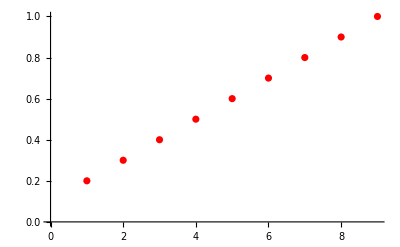

```mathematica
ListPlot[Transpose[Transpose[simutable][[1]]][[2]],PlotStyle->{Red,Thick}]
```

```mathematica
widthtable=Table[{{"d=",d/10},widthinfo[ImageAdjust[Image[convtable[[d]]]],5]},{d,1,10}]
```

{{{d=,1/10},{0.237007,0.134132,0.281874,0.782,0.238109}},{{d=,1/5},{0.254027,0.148584,0.302977,0.874,0.26053}},{{d=,3/10},{0.287598,0.171076,0.33789,0.874,0.296841}},{{d=,2/5},{0.340556,0.199692,0.385566,0.966,0.344479}},{{d=,1/2},{0.412857,0.232539,0.443841,1.058,0.400129}},{{d=,3/5},{0.496184,0.26815,0.509795,1.15,0.460983}},{{d=,7/10},{0.584905,0.305534,0.580588,1.242,0.525156}},{{d=,4/5},{0.676698,0.34409,0.654135,1.334,0.59152}},{{d=,9/10},{0.770429,0.383453,0.729207,1.426,0.659422}},{{d=,1},{0.865463,0.423399,0.805172,1.518,0.728489}}}

```mathematica
Transpose[Transpose[widthtable][[1]]][[2]]
```

{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

```mathematica
Transpose[Transpose[widthtable][[2]]][[1]]
```

{0.237007,0.254027,0.287598,0.340556,0.412857,0.496184,0.584905,0.676698,0.770429,0.865463}

```mathematica
Transpose[Transpose[widthtable][[2]]][[2]]
```

{0.134132,0.148584,0.171076,0.199692,0.232539,0.26815,0.305534,0.34409,0.383453,0.423399}

```mathematica
Transpose[Transpose[widthtable][[2]]][[3]]
```

{0.281874,0.302977,0.33789,0.385566,0.443841,0.509795,0.580588,0.654135,0.729207,0.805172}

```mathematica
Transpose[Transpose[widthtable][[2]]][[4]]
```

{0.782,0.874,0.874,0.966,1.058,1.15,1.242,1.334,1.426,1.518}

```mathematica
Transpose[Transpose[widthtable][[2]]][[5]]
```

{0.238109,0.26053,0.296841,0.344479,0.400129,0.460983,0.525156,0.59152,0.659422,0.728489}

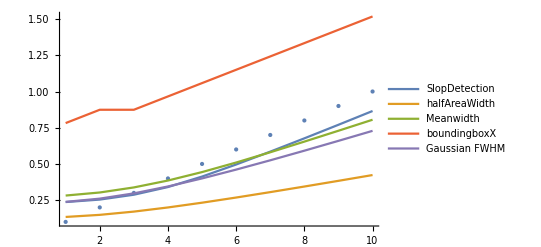

```mathematica
Show[ListPlot[Transpose[Transpose[widthtable][[1]]][[2]],PlotStyle->{PointSize[Large]}],ListLinePlot[{Transpose[Transpose[widthtable][[2]]][[1]],Transpose[Transpose[widthtable][[2]]][[2]],Transpose[Transpose[widthtable][[2]]][[3]],Transpose[Transpose[widthtable][[2]]][[4]],Transpose[Transpose[widthtable][[2]]][[5]]},PlotLegends->{"SlopDetection","halfAreaWidth","Meanwidth","boundingboxX","Gaussian FWHM"}],PlotRange->All]
```

```mathematica
(*

*)
```